## Figure 2

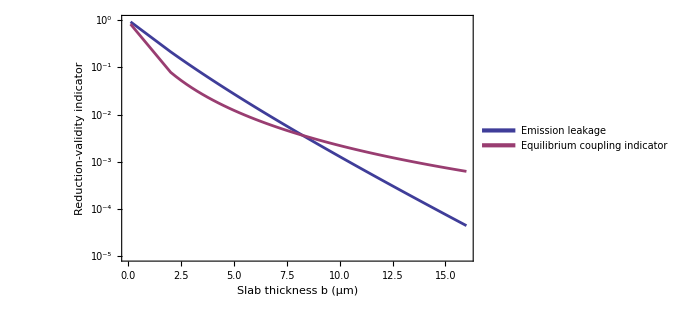

C:/Users/mrkho_000/Desktop/PRE_2026/New_optimization_version/figures_mathematica9_final/Clean_Figs/fig2_opacity_final.pdf

```mathematica
(****************************************)
(*Figure 2: Thickness Indicators*)
(****************************************)
(*Include 0.10 um explicitly because the manuscript contrasts it with the opaque-slab regime.*)

(*Copy and paste the column generated in fig2_opacity.csv*)
opacityRows={{0.0999999999999999,0.9216000138301181,0.823974609375},{2,0.21358589665451883,0.0787172011661807},{2.25,0.17814296772705696,0.064},{2.5,0.1489030997694131,0.052734375},{2.75,0.12471888491788437,0.0439649908406269},{3,0.10466724480308404,0.037037037037037035},{3.25,0.0880031593554244,0.031491471059921276},{3.5,0.0741234320797636,0.027},{3.7499999999999996,0.0625382117415446,0.023323615160349864},{4,0.052848530602408,0.0202854996243426},{4.25,0.0447285266141858,0.017752938275663682},{4.499999999999999,0.0379113251697369,0.015625000000000007},{4.75,0.0321777900746392,0.013824000000000006},{5,0.0273475318157128,0.0122894856622667},{5.25,0.023271697678975408,0.010973936899862825},{5.5,0.0198271730356432,0.00983965014577259},{5.749999999999999,0.0169119038177479,0.00885645167903563},{6,0.014441112584690545,0.008},{6.249999999999999,0.0123442289614503,0.00725051189956698},{6.500000000000001,0.010562392874950073,0.006591796875},{6.75,0.00904641840427114,0.00601051840721262},{6.999999999999999,0.00775512907744091,0.00549562385507836},{7.25,0.00665399353075072,0.00503790087463556},{7.499999999999999,0.00571400469747258,0.00462962962962963},{7.75,0.00491075695760548,0.00426430813574714},{8,0.00422368461103728,0.00393643388249015},{8.249999999999998,0.00363543213741535,0.00364132908511606},{8.5,0.00313133236804613,0.003375},{8.75,0.00269897322239701,0.00313402301185415},{9,0.00232783729151174,0.00291545189504373},{9.25,0.00200900146851595,0.00271674192209491},{9.499999999999998,0.00173488617806455,0.00253568745304282},{9.75,0.00149904565671598,0.00237037037037037},{10,0.00129599227528438,0.00221911728445796},{10.249999999999998,0.00112104914381947,0.00208046386638798},{10.5,0.000970226256804353,0.001953125},{10.749999999999998,0.0008401162656424,0.00183596970649984},{11,0.000727806643575798,0.001728},{11.249999999999998,0.000630805563669484,0.00162833299409729},{11.499999999999998,0.000546979266515013,0.00153618570778334},{11.75,0.000474499069431467,0.00145086212107981},{11.999999999999998,0.000411796478124169,0.00137174211248285},{12.25,0.000357525117085591,0.00129827197595792},{12.499999999999998,0.000310528406260389,0.00122995626822157},{12.749999999999998,0.000269812086575409,0.00116635077999708},{13,0.000234520842299063,0.00110705645987945},{13.249999999999998,0.000203918389090815,0.00105171414798981},{13.5,0.000177370497314319,0.001},{13.749999999999998,0.000154330504220433,0.000951621501359144},{14,0.000134326938829806,0.000906313987445873},{14.249999999999998,0.000116952942116201,0.000863837598531476},{14.499999999999998,0.00010185721435015,0.000823974609375},{14.75,8.87362628057913*10^-5,0.00078652708238507},{14.999999999999998,7.73277577809508*10^-5,0.000751314800901578},{15.25,6.74048341226301*10^-5,0.000718173445536851},{15.5,5.87712000905678*10^-5,0.000686952981884795},{15.75,5.12569361804177*10^-5,0.000657516232431988},{16,4.47148840882959*10^-5,0.000629737609329446}};

(*Clean ticks for the ListLogPlot below*)
yMajorTicks = Table[{10^k, Superscript[10, k], {0.01, 0}}, {k, -5, 1}];
yIntermediateTicks = Flatten[Table[{n*10^k, "", {0.005, 0}}, {k, -5, 1}, {n, 2, 9}], 1];
allYTicks = Join[yMajorTicks, yIntermediateTicks];

(* Ticks for the right frame without labels *)
yMajorTicksRight = Table[{10^k, "", {0.01, 0}}, {k, -5, 1}];
yIntermediateTicksRight = Flatten[Table[{n*10^k, "", {0.005, 0}}, {k, -5,1}, {n, 2, 9}], 1];
allYRightTicks = Join[yMajorTicksRight, yIntermediateTicksRight];

fig2Plot=With[{nLines=2},ListLogPlot[{opacityRows[[All,{1,2}]],opacityRows[[All,{1,3}]]},(*1. Match curves to standard V9 indexing colors and thickness*)PlotStyle->Table[Directive[ColorData[1,i],Thickness[0.004]],{i,nLines}],Joined->True,Frame->True,Axes->False,FrameLabel->{Style["Slab thickness \!\(\*StyleBox[\"b\",FontSlant->\"Italic\"]\) (μm)",FontFamily->"Times",FontSize->15],Style["Reduction-validity indicator",FontFamily->"Times",FontSize->15]},FrameTicksStyle->Directive[FontFamily->"Times",FontSize->15],FrameTicks->{{allYTicks,allYRightTicks},{Automatic,Automatic}},PlotLegends->Placed[LineLegend[(*2. Direct matching styles and custom thickness for the 2 legend lines*)Table[Directive[ColorData[1,i],AbsoluteThickness[3]],{i,nLines}],{"Emission leakage","Equilibrium coupling indicator"},(*3. Provide spatial bounding room for the thickness to render correctly*)LegendMarkerSize->{25,1}],{0.3,0.1}],PlotRange->{10^-5,1},ImageSize->500,BaseStyle->{FontFamily->"Times",FontSize->15},PlotRangePadding->None]]

(***** Export *****)
Export["C:/Users/mrkho_000/Desktop/PRE_2026/New_optimization_version/figures_mathematica9_final/Clean_Figs/fig2_opacity_final.pdf",fig2Plot]
```

## Figure 3

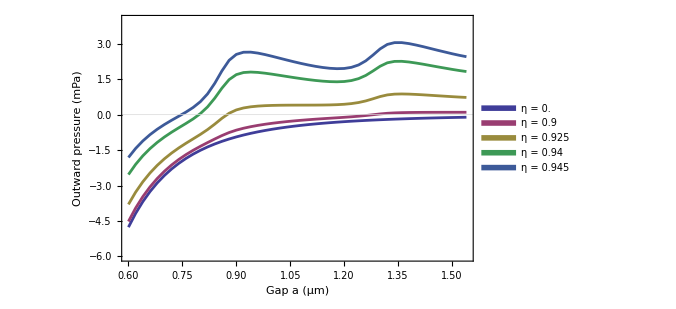

C:/Users/mrkho_000/Desktop/PRE_2026/New_optimization_version/figures_mathematica9_final/Clean_Figs/fig3_pressure_curves_final.pdf

```mathematica
(****************************************)
(*Figure 3: Pressure curves*)
(****************************************)

(*Copy and paste the column generated in fig3_pressure_curves.csv*)

pressureRows={{0.6,0,-4.76382371702811},{0.6,0.9,-4.52188663495621},{0.6,0.925,-3.79917881762499},{0.6,0.94,-2.53667428785855},{0.6,0.945,-1.81287623493988},{0.62,0,-4.17944906195867},{0.62,0.9,-3.95406292752071},{0.62,0.925,-3.28079646690995},{0.62,0.94,-2.10466438693074},{0.62,0.945,-1.43038559899524},{0.64,0,-3.68192070109088},{0.64,0.9,-3.47131250640478},{0.64,0.925,-2.84219268626758},{0.64,0.94,-1.74318927165548},{0.64,0.945,-1.11313345344751},{0.66,0,-3.25620343334216},{0.66,0.9,-3.05862049497112},{0.66,0.925,-2.46841325729185},{0.66,0.94,-1.4374004897295},{0.66,0.945,-0.846331866435401},{0.6799999999999999,0,-2.89021295390896},{0.6799999999999999,0.9,-2.70391780346534},{0.6799999999999999,0.925,-2.14743480163656},{0.6799999999999999,0.94,-1.17535544776944},{0.6799999999999999,0.945,-0.618085087151731},{0.7,0,-2.57417216702979},{0.7,0.9,-2.39739873157358},{0.7,0.925,-1.86936684690997},{0.7,0.94,-0.94701799192992},{0.7,0.945,-0.418274810777587},{0.72,0,-2.30012122730131},{0.72,0.9,-2.13098498853185},{0.72,0.925,-1.62577864427042},{0.72,0.94,-0.74334651089213},{0.72,0.945,-0.23751197409886},{0.74,0,-2.06154158068935},{0.74,0.9,-1.89787640417356},{0.74,0.925,-1.40903140391059},{0.74,0.94,-0.555246561653595},{0.74,0.945,-0.0658729134495484},{0.7599999999999999,0,-1.85306528315239},{0.7599999999999999,0.9,-1.69212921139866},{0.7599999999999999,0.925,-1.21146618194304},{0.7599999999999999,0.94,-0.372080457935064},{0.7599999999999999,0.945,0.1089778189554871},{0.7799999999999999,0,-1.67024863746561},{0.7799999999999999,0.9,-1.50820308901671},{0.7799999999999999,0.925,-1.02427528820119},{0.7799999999999999,0.94,-0.179362857219989},{0.7799999999999999,0.945,0.3047634213619409},{0.7999999999999999,0,-1.50939471817148},{0.7999999999999999,0.9,-1.34047199114845},{0.7999999999999999,0.925,-0.836081017913565},{0.7999999999999999,0.94,0.0442922983381944},{0.7999999999999999,0.945,0.5485853335298129},{0.82,0,-1.3674133302191},{0.82,0.9,-1.18299529465777},{0.82,0.925,-0.632429354555109},{0.82,0.94,0.3282059055213263},{0.82,0.945,0.878284357121624},{0.84,0,-1.24170983082885},{0.84,0.9,-1.03082281123486},{0.84,0.925,-0.401290190681707},{0.84,0.94,0.6969307300985923},{0.84,0.945,1.3256800964537916},{0.86,0,-1.13009635384067},{0.86,0.9,-0.885128504082046},{0.86,0.925,-0.153780625398432},{0.86,0.94,1.1223356503200679},{0.86,0.945,1.853090569535539},{0.88,0,-1.03072053148631},{0.88,0.9,-0.757287413792817},{0.88,0.925,0.059220179903472295},{0.88,0.94,1.4845642761748234},{0.88,0.945,2.301135125218522},{0.8999999999999999,0,-0.942007964386398},{0.8999999999999999,0.9,-0.655465920046652},{0.8999999999999999,0.925,0.20032438588023901},{0.8999999999999999,0.94,1.694736819827675},{0.8999999999999999,0.945,2.5511592988192278},{0.9199999999999999,0,-0.8626155555797},{0.9199999999999999,0.9,-0.575144164456426},{0.9199999999999999,0.925,0.2834959135829221},{0.9199999999999999,0.94,1.7831509443517954},{0.9199999999999999,0.945,2.6427302905066656},{0.94,0,-0.791393476189975},{0.94,0.9,-0.509473223654812},{0.94,0.925,0.33262450187823106},{0.94,0.94,1.8035245839636067},{0.94,0.945,2.646700484752572},{0.96,0,-0.727354024702527},{0.96,0.9,-0.454036753238972},{0.96,0.925,0.3623843484399703},{0.96,0.94,1.7885085389074775},{0.96,0.945,2.606059386160876},{0.98,0,-0.669646019132347},{0.98,0.9,-0.406232619449355},{0.98,0.925,0.38061626289438655},{0.98,0.94,1.7551248267565567},{0.98,0.945,2.54310964169946},{1,0,-0.61753365106014},{1,0.9,-0.364431222595616},{1,0.925,0.3916236808918538},{1,0.94,1.7123619241736274},{1,0.945,2.4695337447498606},{1.02,0,-0.570378954210717},{1.02,0.9,-0.327504655271132},{1.02,0.925,0.3980003393744776},{1.02,0.94,1.6653824736092597},{1.02,0.945,2.3919718232507288},{1.04,0,-0.527627213932356},{1.04,0.9,-0.294612049605125},{1.04,0.925,0.40144301027319473},{1.04,0.94,1.617382424474698},{1.04,0.945,2.3144815872707882},{1.06,0,-0.488794779496587},{1.06,0.9,-0.265129911803197},{1.06,0.925,0.4029929006467471},{1.06,0.94,1.5701326108878162},{1.06,0.945,2.2392521226693747},{1.08,0,-0.453458847476918},{1.08,0.9,-0.238492286476354},{1.08,0.925,0.4036444851405386},{1.08,0.94,1.525379352660441},{1.08,0.945,2.1684626737431287},{1.1,0,-0.421248868284995},{1.1,0.9,-0.214245612763868},{1.1,0.925,0.40409821532606804},{1.1,0.94,1.4842504929975726},{1.1,0.945,2.103483850324948},{1.1199999999999999,0,-0.391839294319812},{1.1199999999999999,0.9,-0.191963944730699},{1.1199999999999999,0.925,0.40507969888851764},{1.1199999999999999,0.94,1.4479943152088455},{1.1199999999999999,0.945,2.045863178155002},{1.1400000000000001,0,-0.364943440984571},{1.1400000000000001,0.9,-0.171164891650795},{1.1400000000000001,0.925,0.40765451332197095},{1.1400000000000001,0.94,1.4186900486456502},{1.1400000000000001,0.945,1.9982580689401723},{1.16,0,-0.34030827400512},{1.16,0.9,-0.151417050217995},{1.16,0.925,0.4127839153090451},{1.16,0.94,1.3982140182294636},{1.16,0.945,1.9630635022690792},{1.1800000000000002,0,-0.317709970318985},{1.1800000000000002,0.9,-0.132003867512464},{1.1800000000000002,0.925,0.42265335170909546},{1.1800000000000002,0.94,1.3913070403739838},{1.1800000000000002,0.945,1.9464792134529136},{1.2,0,-0.296950127054181},{1.2,0.9,-0.112194315137572},{1.2,0.925,0.4395781715547566},{1.2,0.94,1.4030281136551286},{1.2,0.945,1.95512348143271},{1.22,0,-0.277852515148117},{1.22,0.9,-0.0906972398013521},{1.22,0.925,0.46817587972008684},{1.22,0.94,1.4437906611079487},{1.22,0.945,2.002723921663967},{1.24,0,-0.260260292034964},{1.24,0.9,-0.0661413102529},{1.24,0.925,0.5134457870853033},{1.24,0.94,1.524931744099561},{1.24,0.945,2.104250825236712},{1.26,0,-0.244033602389594},{1.26,0.9,-0.036939564537981},{1.26,0.925,0.5813197879154501},{1.26,0.94,1.6600519613252727},{1.26,0.945,2.277745471696761},{1.28,0,-0.229047507814837},{1.28,0.9,-0.00313405198538632},{1.28,0.925,0.67131354868843},{1.28,0.94,1.8480968526604593},{1.28,0.945,2.521942173250289},{1.2999999999999998,0,-0.215190196115121},{1.2999999999999998,0.9,0.031100008437954196},{1.2999999999999998,0.925,0.7664884419131823},{1.2999999999999998,0.94,2.0499859352157066},{1.2999999999999998,0.945,2.7851559554271703},{1.32,0,-0.202361428825416},{1.32,0.9,0.0582368880380488},{1.32,0.925,0.8364887028461173},{1.32,0.94,2.195304060453915},{1.32,0.945,2.9739052714394343},{1.3399999999999999,0,-0.190471192287237},{1.3399999999999999,0.9,0.0752546263372233},{1.3399999999999999,0.925,0.8689106241219019},{1.3399999999999999,0.94,2.2549496965567104},{1.3399999999999999,0.945,3.0493382095745307},{1.36,0,-0.179438523045308},{1.36,0.9,0.085401244998512},{1.36,0.925,0.8764613402010775},{1.36,0.94,2.258148315045581},{1.36,0.945,3.050146400423889},{1.38,0,-0.169190482889239},{1.38,0.9,0.0914183052603826},{1.38,0.925,0.8698683260158846},{1.38,0.94,2.2296294192854518},{1.38,0.945,3.0091162517938064},{1.4,0,-0.159661262653044},{1.4,0.9,0.0950668032374393},{1.4,0.925,0.8559636345289561},{1.4,0.94,2.185109488032918},{1.4,0.945,2.9470722905682103},{1.42,0,-0.150791397048114},{1.42,0.9,0.0974902017982706},{1.42,0.925,0.8391413449492203},{1.42,0.94,2.134706333131382},{1.42,0.945,2.8774398031480817},{1.44,0,-0.142527075452671},{1.44,0.9,0.0988197303348483},{1.44,0.925,0.8197595616505614},{1.44,0.94,2.079158636648381},{1.44,0.945,2.801166641562463},{1.46,0,-0.134819535802511},{1.46,0.9,0.0996617075651603},{1.46,0.925,0.8000929108098184},{1.46,0.94,2.0236652089230245},{1.46,0.945,2.725133525744095},{1.48,0,-0.127624530597221},{1.48,0.9,0.10031100700339264},{1.48,0.925,0.7811914968931981},{1.48,0.94,1.970619335412475},{1.48,0.945,2.652517651251381},{1.5,0,-0.120901855612759},{1.5,0.9,0.10051647711168019},{1.5,0.925,0.7619251636510986},{1.5,0.94,1.9173241000321561},{1.5,0.945,2.5797059461416887},{1.5199999999999998,0,-0.114614933244244},{1.5199999999999998,0.9,0.10080364563733783},{1.5199999999999998,0.925,0.7442831227720932},{1.5199999999999998,0.94,1.868336606694907},{1.5199999999999998,0.945,2.512733850616266},{1.54,0,-0.108730443532472},{1.54,0.9,0.1013521927053757},{1.54,0.925,0.728886850698172},{1.54,0.94,1.8250668732435473},{1.54,0.945,2.4534732449350387}};

aVals=Range[0.60*10^-6,1.55*10^-6,0.02*10^-6];
etaVals={0.,0.90,0.925,0.94,0.945};

fig3Plot=With[{nLines=Length[etaVals]},ListLinePlot[Table[Select[pressureRows,#[[2]]==eta&][[All,{1,3}]],{eta,etaVals}],(*1. Apply matching colors and thickness to the curves*)PlotStyle->Table[Directive[ColorData[1,i],Thickness[0.004]],{i,nLines}],Frame->True,GridLines->{None,{0}},Axes->False,FrameLabel->{Style["Gap \!\(\*StyleBox[\"a\",FontSlant->\"Italic\"]\) (μm)",FontFamily->"Times",FontSize->15],Style["Outward pressure (mPa)",FontFamily->"Times",FontSize->15]},FrameTicksStyle->Directive[FontFamily->"Times",FontSize->15],PlotLegends->Placed[LineLegend[(*2. Apply the exact same style directives directly to the legend entries*)Table[Directive[ColorData[1,i],AbsoluteThickness[4]],{i,nLines}],Map[Function[x,"η = "<>ToString[x]],etaVals],LegendMarkerSize->{25,1}],{0.85,0.27}],PlotRange->{-6,4},ImageSize->500,BaseStyle->{FontFamily->"Times",FontSize->15},PlotRangePadding->None]]

(*Export*)
Export["C:/Users/mrkho_000/Desktop/PRE_2026/New_optimization_version/figures_mathematica9_final/Clean_Figs/fig3_pressure_curves_final.pdf",fig3Plot]
```

## Figure 4

```mathematica
(****************************************)(*Standalone Mathematica 9 code for Figure 4.*)(*The five columns of coarse are:*)(*{a0[m],eta0,four-corner robust pressure[Pa],*)(*robust cavity excess[Pa],cavity-constraint pass flag}.*)(****************************************)coarse={{2.5*10^-7,0.85,-0.182249385358806,-0.182260267708673,0},{2.75*10^-7,0.85,-0.123074319221306,-0.123085201571173,0},{3.*10^-7,0.85,-0.0860721734025319,-0.0860830557523989,0},{3.25*10^-7,0.85,-0.0619823289565542,-0.0619932113064212,0},{3.5*10^-7,0.85,-0.0457571655199199,-0.045768047869787,0},{3.75*10^-7,0.85,-0.0345074982636183,-0.0345183806134854,0},{4.*10^-7,0.85,-0.0265092470046382,-0.0265201293545052,0},{4.25*10^-7,0.85,-0.0206960600413244,-0.0207069423911914,0},{4.5000000000000003*10^-7,0.85,-0.0163892187162731,-0.0164001010661401,0},{4.75*10^-7,0.85,-0.0131459827221656,-0.0131568650720326,0},{5.000000000000001*10^-7,0.85,-0.0106670209504673,-0.0106779033003343,0},{5.250000000000001*10^-7,0.85,-0.00874580776749008,-0.00875669011735711,0},{5.5*10^-7,0.85,-0.00723814324726075,-0.00724902559712777,0},{5.75*10^-7,0.85,-0.00604159639815571,-0.00605247874802273,0},{6.*10^-7,0.85,-0.00508218490905516,-0.00509306725892218,0},{6.25*10^-7,0.85,-0.00430567233951888,-0.0043165546893859,0},{6.5*10^-7,0.85,-0.00367175997770933,-0.00368264232757635,0},{6.750000000000001*10^-7,0.85,-0.00315013520059077,-0.00316101755045779,0},{7.000000000000001*10^-7,0.85,-0.00271773680735333,-0.00272861915722035,0},{7.25*10^-7,0.85,-0.00235683248640419,-0.00236771483627121,0},{7.5*10^-7,0.85,-0.00205364541842527,-0.00206452776829229,0},{7.75*10^-7,0.85,-0.0017973536762314,-0.00180823602609842,0},{8.*10^-7,0.85,-0.00157934044950682,-0.00159022279937384,0},{8.249999999999999*10^-7,0.85,-0.00139262459146644,-0.00140350694133346,0},{8.500000000000001*10^-7,0.85,-0.00123153406666624,-0.00124241641653326,0},{8.750000000000001*10^-7,0.85,-0.00109195268102641,-0.00110283503089343,0},{9.000000000000001*10^-7,0.85,-0.000971519182860286,-0.000982401532727307,0},{9.25*10^-7,0.85,-0.000867759452926668,-0.000878641802793689,0},{9.5*10^-7,0.85,-0.000777791896009023,-0.000788674245876044,0},{9.75*10^-7,0.85,-0.000699293239169198,-0.000710175589036219,0},{1.0000000000000002*10^-6,0.85,-0.000630472623890784,-0.000641354973757805,0},{1.025*10^-6,0.85,-0.000569895137815368,-0.000580777487682389,0},{1.0500000000000001*10^-6,0.85,-0.000516384711882012,-0.000527267061749034,0},{1.075*10^-6,0.85,-0.000468966512909957,-0.000479848862776979,0},{1.1*10^-6,0.85,-0.000426810036575356,-0.000437692386442377,0},{1.125*10^-6,0.85,-0.000389219906997205,-0.000400102256864226,0},{1.15*10^-6,0.85,-0.000355596465154122,-0.000366478815021143,0},{1.1750000000000002*10^-6,0.85,-0.000325407167956876,-0.000336289517823898,0},{1.2000000000000002*10^-6,0.85,-0.000298193968826098,-0.00030907631869312,0},{1.2250000000000001*10^-6,0.85,-0.00027349459431916,-0.000284376944186181,0},{1.25*10^-6,0.85,-0.000250896564445194,-0.000261778914312215,0},{1.275*10^-6,0.85,-0.000229976298897317,-0.000240858648764339,0},{1.3*10^-6,0.85,-0.000210579941507628,-0.000221462291374649,0},{1.325*10^-6,0.85,-0.000193035484901874,-0.000203917834768895,0},{1.35*10^-6,0.85,-0.000177645128671584,-0.000188527478538606,0},{1.375*10^-6,0.85,-0.000164075755337198,-0.000174958105204219,0},{1.4*10^-6,0.85,-0.000151894536041856,-0.000162776885908877,0},{1.4250000000000001*10^-6,0.85,-0.000140898262499595,-0.000151780612366616,0},{1.45*10^-6,0.85,-0.000130883626596122,-0.000141765976463143,0},{1.4750000000000003*10^-6,0.85,-0.000121733252369796,-0.000132615602236818,0},{1.5*10^-6,0.85,-0.000113378990874823,-0.000124261340741844,0},{2.5*10^-7,0.855,-0.182248237160227,-0.182262570471899,0},{2.75*10^-7,0.855,-0.123073209920869,-0.123087543232542,0},{3.*10^-7,0.855,-0.0860710455802826,-0.0860853788919549,0},{3.25*10^-7,0.855,-0.0619811192914629,-0.0619954526031352,0},{3.5*10^-7,0.855,-0.0457557838322984,-0.0457701171439707,0},{3.75*10^-7,0.855,-0.0345057870528669,-0.0345201203645392,0},{4.*10^-7,0.855,-0.0265068987332333,-0.0265212320449057,0},{4.25*10^-7,0.855,-0.0206925701096243,-0.0207069034212966,0},{4.5000000000000003*10^-7,0.855,-0.0163844101282587,-0.016398743439931,0},{4.75*10^-7,0.855,-0.0131405707244619,-0.0131549040361342,0},{5.000000000000001*10^-7,0.855,-0.010661673581756,-0.0106760068934283,0},{5.250000000000001*10^-7,0.855,-0.00874079385389546,-0.00875512716556777,0},{5.5*10^-7,0.855,-0.00723353432551353,-0.00724786763718584,0},{5.75*10^-7,0.855,-0.00603738858308529,-0.0060517218947576,0},{6.*10^-7,0.855,-0.00507834675016844,-0.00509268006184075,0},{6.25*10^-7,0.855,-0.00430216336555109,-0.0043164966772234,0},{6.5*10^-7,0.855,-0.0036685378467624,-0.00368287115843471,0},{6.750000000000001*10^-7,0.855,-0.00314715800564495,-0.00316149131731726,0},{7.000000000000001*10^-7,0.855,-0.00271496291577931,-0.00272929622745162,0},{7.25*10^-7,0.855,-0.00235421848179242,-0.00236855179346473,0},{7.5*10^-7,0.855,-0.00205114142069057,-0.00206547473236288,0},{7.75*10^-7,0.855,-0.00179489354806436,-0.00180922685973667,0},{8.*10^-7,0.855,-0.00157682198272624,-0.00159115529439855,0},{8.249999999999999*10^-7,0.855,-0.00138987704154695,-0.00140421035321926,0},{8.500000000000001*10^-7,0.855,-0.00122830720041409,-0.0012426405120864,0},{8.750000000000001*10^-7,0.855,-0.00108807809217004,-0.00110241140384235,0},{9.000000000000001*10^-7,0.855,-0.000967206088849047,-0.000981539400521357,0},{9.25*10^-7,0.855,-0.000863352714480698,-0.000877686026153008,0},{9.5*10^-7,0.855,-0.000773478616756084,-0.000787811928428394,0},{9.75*10^-7,0.855,-0.000695148283547253,-0.000709481595219563,0},{1.0000000000000002*10^-6,0.855,-0.000626521438127584,-0.000640854749799894,0},{1.025*10^-6,0.855,-0.000566140688372615,-0.000580474000044924,0},{1.0500000000000001*10^-6,0.855,-0.000512819531102142,-0.000527152842774452,0},{1.075*10^-6,0.855,-0.000465579142010652,-0.000479912453682961,0},{1.1*10^-6,0.855,-0.000423583568317329,-0.000437916879989639,0},{1.125*10^-6,0.855,-0.00038613578307492,-0.00040046909474723,0},{1.15*10^-6,0.855,-0.00035263238909019,-0.0003669657007625,0},{1.1750000000000002*10^-6,0.855,-0.000322531329580796,-0.000336864641253106,0},{1.2000000000000002*10^-6,0.855,-0.000295366006111125,-0.000309699317783435,0},{1.2250000000000001*10^-6,0.855,-0.000270645199575206,-0.000284978511247516,0},{1.25*10^-6,0.855,-0.000247927196558069,-0.000262260508230379,0},{1.275*10^-6,0.855,-0.000226742043843481,-0.000241075355515791,0},{1.3*10^-6,0.855,-0.00020696347195941,-0.00022129678363172,0},{1.325*10^-6,0.855,-0.000189090007435253,-0.000203423319107563,0},{1.35*10^-6,0.855,-0.000173577783536407,-0.000187911095208717,0},{1.375*10^-6,0.855,-0.000160038905687251,-0.000174372217359561,0},{1.4*10^-6,0.855,-0.000147947917254209,-0.000162281228926519,0},{1.4250000000000001*10^-6,0.855,-0.000137076434621457,-0.000151409746293767,0},{1.45*10^-6,0.855,-0.000127191299555445,-0.000141524611227755,0},{1.4750000000000003*10^-6,0.855,-0.000118168510327366,-0.000132501821999676,0},{1.5*10^-6,0.855,-0.000109945405676851,-0.000124278717349161,0},{2.5*10^-7,0.86,-0.182246724789167,-0.182265603597063,0},{2.75*10^-7,0.86,-0.123071748785748,-0.123090627593644,0},{3.*10^-7,0.86,-0.0860695600494671,-0.0860884388573632,0},{3.25*10^-7,0.86,-0.0619795259608224,-0.0619984047687185,0},{3.5*10^-7,0.86,-0.0457539639207641,-0.0457728427286602,0},{3.75*10^-7,0.86,-0.0345035331074308,-0.0345224119153269,0},{4.*10^-7,0.86,-0.0265038056788517,-0.0265226844867478,0},{4.25*10^-7,0.86,-0.0206879733046654,-0.0207068521125615,0},{4.5000000000000003*10^-7,0.86,-0.0163780764250374,-0.0163969552329335,0},{4.75*10^-7,0.86,-0.0131334422162807,-0.0131523210241768,0},{5.000000000000001*10^-7,0.86,-0.0106546301941736,-0.0106735090020697,0},{5.250000000000001*10^-7,0.86,-0.00873418968031972,-0.00875306848821583,0},{5.5*10^-7,0.86,-0.00722746359363261,-0.00724634240152872,0},{5.75*10^-7,0.86,-0.00603184617622807,-0.00605072498412419,0},{6.*10^-7,0.86,-0.00507329124307646,-0.00509217005097258,0},{6.25*10^-7,0.86,-0.0042975414509154,-0.00431642025881151,0},{6.5*10^-7,0.86,-0.00366429375326644,-0.00368317256116256,0},{6.750000000000001*10^-7,0.86,-0.0031432365347696,-0.00316211534266572,0},{7.000000000000001*10^-7,0.86,-0.00271130923046112,-0.00273018803835723,0},{7.25*10^-7,0.86,-0.00235077539553353,-0.00236965420342965,0},{7.5*10^-7,0.86,-0.00204784323348269,-0.0020667220413788,0},{7.75*10^-7,0.86,-0.0017916531469202,-0.00181053195481631,0},{8.*10^-7,0.86,-0.00157350474423245,-0.00159238355212856,0},{8.249999999999999*10^-7,0.86,-0.00138625806928048,-0.0014051368771766,0},{8.500000000000001*10^-7,0.86,-0.00122405689497385,-0.00124293570286997,0},{8.750000000000001*10^-7,0.86,-0.001082974623907,-0.00110185343180312,0},{9.000000000000001*10^-7,0.86,-0.000961525024494137,-0.000980403832390251,0},{9.25*10^-7,0.86,-0.000857548297590984,-0.000876427105487098,0},{9.5*10^-7,0.86,-0.000767797298227282,-0.000786676106123396,0},{9.75*10^-7,0.86,-0.000689688674288679,-0.000708567482184793,0},{1.0000000000000002*10^-6,0.86,-0.000621317055954838,-0.000640195863850952,0},{1.025*10^-6,0.86,-0.00056119544099286,-0.000580074248888974,0},{1.0500000000000001*10^-6,0.86,-0.000508123582595006,-0.00052700239049112,0},{1.075*10^-6,0.86,-0.000461117399465562,-0.000479996207361677,0},{1.1*10^-6,0.86,-0.000419333762090571,-0.000438212569986685,0},{1.125*10^-6,0.86,-0.000382073469065539,-0.000400952276961653,0},{1.15*10^-6,0.86,-0.000348728199358196,-0.00036760700725431,0},{1.1750000000000002*10^-6,0.86,-0.000318743365359644,-0.000337622173255758,0},{1.2000000000000002*10^-6,0.86,-0.000291641104953379,-0.000310519912849493,0},{1.2250000000000001*10^-6,0.86,-0.000266892073158911,-0.000285770881055025,0},{1.25*10^-6,0.86,-0.000244016051610467,-0.000262894859506581,0},{1.275*10^-6,0.86,-0.000222482003579034,-0.000241360811475148,0},{1.3*10^-6,0.86,-0.000202199989597051,-0.000221078797493165,0},{1.325*10^-6,0.86,-0.000183893157439045,-0.000202771965335159,0},{1.35*10^-6,0.86,-0.000168220405799532,-0.000187099213695646,0},{1.375*10^-6,0.86,-0.000154721692458615,-0.000173600500354729,0},{1.4*10^-6,0.86,-0.00014274955146971,-0.000161628359365824,0},{1.4250000000000001*10^-6,0.86,-0.000132042438883958,-0.000150921246780072,0},{1.45*10^-6,0.86,-0.000122327878207336,-0.00014120668610345,0},{1.4750000000000003*10^-6,0.86,-0.000113473139639884,-0.000132351947535998,0},{1.5*10^-6,0.86,-0.000105422791181965,-0.00012430159907808,0},{2.5*10^-7,0.865,-0.182244732697021,-0.182269598819768,0},{2.75*10^-7,0.865,-0.123069824182395,-0.123094690305142,0},{3.*10^-7,0.865,-0.0860676033132917,-0.0860924694360383,0},{3.25*10^-7,0.865,-0.0619774272326545,-0.0620022933554011,0},{3.5*10^-7,0.865,-0.0457515667437716,-0.0457764328665182,0},{3.75*10^-7,0.865,-0.0345005642280971,-0.0345254303508438,0},{4.*10^-7,0.865,-0.0264997315395752,-0.0265245976623219,0},{4.25*10^-7,0.865,-0.0206819184428059,-0.0207067845655525,0},{4.5000000000000003*10^-7,0.865,-0.0163697337144743,-0.0163945998372209,0},{4.75*10^-7,0.865,-0.0131240525681871,-0.0131489186909337,0},{5.000000000000001*10^-7,0.865,-0.0106453526551779,-0.0106702187779245,0},{5.250000000000001*10^-7,0.865,-0.00872549066865024,-0.00875035679139685,0},{5.5*10^-7,0.865,-0.00721946722885929,-0.00724433335160591,0},{5.75*10^-7,0.865,-0.00602454571998913,-0.00604941184273574,0},{6.*10^-7,0.865,-0.00506663213069735,-0.00509149825344397,0},{6.25*10^-7,0.865,-0.00429145346640698,-0.0043163195891536,0},{6.5*10^-7,0.865,-0.00365870343493527,-0.00368356955768189,0},{6.750000000000001*10^-7,0.865,-0.00313807117539147,-0.00316293729813809,0},{7.000000000000001*10^-7,0.865,-0.00270649659898499,-0.0027313627217316,0},{7.25*10^-7,0.865,-0.00234624016642002,-0.00237110628916664,0},{7.5*10^-7,0.865,-0.00204349886762945,-0.00206836499037606,0},{7.75*10^-7,0.865,-0.00178738490100335,-0.00181225102374996,0},{8.*10^-7,0.865,-0.00156913529601057,-0.00159400141875719,0},{8.249999999999999*10^-7,0.865,-0.00138149119065829,-0.00140635731340491,0},{8.500000000000001*10^-7,0.865,-0.00121845843809097,-0.00124332456083759,0},{8.750000000000001*10^-7,0.865,-0.0010762523774885,-0.00110111850023512,0},{9.000000000000001*10^-7,0.865,-0.000954041950757828,-0.000978908073504443,0},{9.25*10^-7,0.865,-0.000849902731944337,-0.000874768854690952,0},{9.5*10^-7,0.865,-0.000760313872032685,-0.0007851799947793,0},{9.75*10^-7,0.865,-0.000682497280807297,-0.000707363403553912,0},{1.0000000000000002*10^-6,0.865,-0.000614461846251986,-0.000639327968998601,0},{1.025*10^-6,0.865,-0.000554681562946875,-0.00057954768569349,0},{1.0500000000000001*10^-6,0.865,-0.000501938080773351,-0.000526804203519966,0},{1.075*10^-6,0.865,-0.000455240393927959,-0.000480106516674574,0},{1.1*10^-6,0.865,-0.000413735919376395,-0.00043860204212301,0},{1.125*10^-6,0.865,-0.000376722592001101,-0.000401588714747716,0},{1.15*10^-6,0.865,-0.00034358560503524,-0.000368451727781854,0},{1.1750000000000002*10^-6,0.865,-0.000313753865829461,-0.000338619988576076,0},{1.2000000000000002*10^-6,0.865,-0.000286734676732456,-0.000311600799479071,0},{1.2250000000000001*10^-6,0.865,-0.000261948474206385,-0.000286814596953,0},{1.25*10^-6,0.865,-0.000238864321928312,-0.000263730444674927,0},{1.275*10^-6,0.865,-0.000216870719620933,-0.000241736842367548,0},{1.3*10^-6,0.865,-0.000195925570654501,-0.000220791693401116,0},{1.325*10^-6,0.865,-0.000177047892331777,-0.000201914015078391,0},{1.35*10^-6,0.865,-0.000161163680894351,-0.000186029803640966,0},{1.375*10^-6,0.865,-0.000147717866636148,-0.000172583989382763,0},{1.4*10^-6,0.865,-0.000135902268123215,-0.00016076839086983,0},{1.4250000000000001*10^-6,0.865,-0.00012541166236934,-0.000150277785115955,0},{1.45*10^-6,0.865,-0.00011592178186695,-0.000140787904613565,0},{1.4750000000000003*10^-6,0.865,-0.000107288398797066,-0.000132154521543681,0},{1.5*10^-6,0.865,-9.94656053567041*^-5,-0.000124331728103319,0},{2.5*10^-7,0.87,-0.18224210863992,-0.18227486146773,0},{2.75*10^-7,0.87,-0.123067289025608,-0.123100041853418,0},{3.*10^-7,0.87,-0.0860650258319391,-0.0860977786597486,0},{3.25*10^-7,0.87,-0.0619746627172111,-0.0620074155450205,0},{3.5*10^-7,0.87,-0.045748409105889,-0.0457811619336985,0},{3.75*10^-7,0.87,-0.0344966535336896,-0.0345294063614991,0},{4.*10^-7,0.87,-0.0264943649781009,-0.0265271178059104,0},{4.25*10^-7,0.87,-0.0206739428261068,-0.0207066956539163,0},{4.5000000000000003*10^-7,0.87,-0.016358744442291,-0.0163914972701005,0},{4.75*10^-7,0.87,-0.0131116841931433,-0.0131444370209528,0},{5.000000000000001*10^-7,0.87,-0.0106331319342634,-0.0106658847620728,0},{5.250000000000001*10^-7,0.87,-0.00871403199743839,-0.00874678482524786,0},{5.5*10^-7,0.87,-0.00720893410750269,-0.00724168693531216,0},{5.75*10^-7,0.87,-0.00601492927473763,-0.00604768210254711,0},{6.*10^-7,0.87,-0.00505786048798271,-0.00509061331579218,0},{6.25*10^-7,0.87,-0.00428343413565027,-0.00431618696345974,0},{6.5*10^-7,0.87,-0.00365133964999089,-0.00368409247780036,0},{6.750000000000001*10^-7,0.87,-0.00313126716389663,-0.0031640199917061,0},{7.000000000000001*10^-7,0.87,-0.00270015721592157,-0.00273291004373105,0},{7.25*10^-7,0.87,-0.00234026619091169,-0.00237301901872116,0},{7.5*10^-7,0.87,-0.00203777630860371,-0.00207052913641318,0},{7.75*10^-7,0.87,-0.0017817626173308,-0.00181451544514027,0},{8.*10^-7,0.87,-0.00156337971829401,-0.00159613254610348,0},{8.249999999999999*10^-7,0.87,-0.00137521212506508,-0.00140796495287456,0},{8.500000000000001*10^-7,0.87,-0.00121108400875653,-0.001243836836566,0},{8.750000000000001*10^-7,0.87,-0.00106739764224997,-0.00110015047005945,0},{9.000000000000001*10^-7,0.87,-0.00094418499298403,-0.000976937820793503,0},{9.25*10^-7,0.87,-0.000839831712681793,-0.000872584540491266,0},{9.5*10^-7,0.87,-0.000750456419344883,-0.000783209247154356,0},{9.75*10^-7,0.87,-0.000673024500375759,-0.000705777328185232,0},{1.0000000000000002*10^-6,0.87,-0.000605431898027697,-0.000638184725837169,0},{1.025*10^-6,0.87,-0.000546101229039822,-0.000578854056849295,0},{1.0500000000000001*10^-6,0.87,-0.000493790296543431,-0.000526543124352904,0},{1.075*10^-6,0.87,-0.000447498973499942,-0.000480251801309415,0},{1.1*10^-6,0.87,-0.000406362223757089,-0.000439115051566561,0},{1.125*10^-6,0.87,-0.0003696742108379,-0.000402427038647373,0},{1.15*10^-6,0.87,-0.000336811584616764,-0.000369564412426236,0},{1.1750000000000002*10^-6,0.87,-0.000307181512333305,-0.000339934340142778,0},{1.2000000000000002*10^-6,0.87,-0.000280271756094773,-0.000313024583904246,0},{1.2250000000000001*10^-6,0.87,-0.000255436603964697,-0.00028818943177417,0},{1.25*10^-6,0.87,-0.000232078313252694,-0.000264831141062166,0},{1.275*10^-6,0.87,-0.000209479386384175,-0.000242232214193648,0},{1.3*10^-6,0.87,-0.000187660728039788,-0.000220413555849261,0},{1.325*10^-6,0.87,-0.000168031083796751,-0.000200783911606224,0},{1.35*10^-6,0.87,-0.000151868307212188,-0.000184621135021661,0},{1.375*10^-6,0.87,-0.00013849216398229,-0.000171244991791763,0},{1.4*10^-6,0.87,-0.000126882763531787,-0.00015963559134126,0},{1.4250000000000001*10^-6,0.87,-0.000116677346695897,-0.00014943017450537,0},{1.45*10^-6,0.87,-0.000107483423065326,-0.000140236250874799,0},{1.4750000000000003*10^-6,0.87,-9.91416167412209*^-5,-0.000131894444550693,0},{1.5*10^-6,0.87,-9.16185687162463*^-5,-0.000124371396525718,0},{2.5*10^-7,0.875,-0.182238652001176,-0.182281793879185,0},{2.75*10^-7,0.875,-0.123063949496935,-0.123107091374945,0},{3.*10^-7,0.875,-0.0860616305530471,-0.0861047724310569,0},{3.25*10^-7,0.875,-0.0619710210657534,-0.0620141629437632,0},{3.5*10^-7,0.875,-0.0457442496082504,-0.0457873914862602,0},{3.75*10^-7,0.875,-0.0344915020625934,-0.0345346439406031,0},{4.*10^-7,0.875,-0.0264872957490861,-0.0265304376270959,0},{4.25*10^-7,0.875,-0.0206634367643317,-0.0207065786423414,0},{4.5000000000000003*10^-7,0.875,-0.0163442684990993,-0.0163874103771091,0},{4.75*10^-7,0.875,-0.0130953915081019,-0.0131385333861117,0},{5.000000000000001*10^-7,0.875,-0.0106170337173453,-0.0106601755953551,0},{5.250000000000001*10^-7,0.875,-0.00869893760588439,-0.00874207948389414,0},{5.5*10^-7,0.875,-0.00719505892726312,-0.00723820080527287,0},{5.75*10^-7,0.875,-0.00600226162046398,-0.00604540349847373,0},{6.*10^-7,0.875,-0.00504630568327741,-0.00508944756128715,0},{6.25*10^-7,0.875,-0.00427287034466906,-0.0043160122226788,0},{6.5*10^-7,0.875,-0.00364163940438061,-0.00368478128239035,0},{6.750000000000001*10^-7,0.875,-0.00312230430434685,-0.0031654461823566,0},{7.000000000000001*10^-7,0.875,-0.00269180640970961,-0.00273494828771936,0},{7.25*10^-7,0.875,-0.00233239673678371,-0.00237553861479346,0},{7.5*10^-7,0.875,-0.00203023804995717,-0.00207337992796692,0},{7.75*10^-7,0.875,-0.0017743564629862,-0.00181749834099594,0},{8.*10^-7,0.875,-0.00155579800049044,-0.00159893987850018,0},{8.249999999999999*10^-7,0.875,-0.00136694086130428,-0.00141008273931403,0},{8.500000000000001*10^-7,0.875,-0.00120136987330731,-0.00124451175131706,0},{8.750000000000001*10^-7,0.875,-0.00105573350215304,-0.00109887538016278,0},{9.000000000000001*10^-7,0.875,-0.000931200580348178,-0.000974342458357922,0},{9.25*10^-7,0.875,-0.000826565282708324,-0.000869707160718068,0},{9.5*10^-7,0.875,-0.000737471301593384,-0.000780613179603128,0},{9.75*10^-7,0.875,-0.000660546099832978,-0.000703687977842722,0},{1.0000000000000002*10^-6,0.875,-0.00059353683250693,-0.000636678710516674,0},{1.025*10^-6,0.875,-0.000534798434502368,-0.000577940312512112,0},{1.0500000000000001*10^-6,0.875,-0.00048305729521592,-0.000526199173225664,0},{1.075*10^-6,0.875,-0.000437301272283679,-0.000480443150293423,0},{1.1*10^-6,0.875,-0.000396648924182385,-0.000439790802192129,0},{1.125*10^-6,0.875,-0.000360389447907173,-0.000403531325916917,0},{1.15*10^-6,0.875,-0.000327888239077068,-0.000371030117086812,0},{1.1750000000000002*10^-6,0.875,-0.000298523828569785,-0.000341665706579529,0},{1.2000000000000002*10^-6,0.875,-0.000271758241267635,-0.000314900119277379,0},{1.2250000000000001*10^-6,0.875,-0.000246858631061345,-0.000290000509071089,0},{1.25*10^-6,0.875,-0.000223139254108767,-0.000266281132118511,0},{1.275*10^-6,0.875,-0.000199742970429854,-0.000242884848439598,0},{1.3*10^-6,0.875,-0.000176773642538741,-0.000219915520548485,0},{1.325*10^-6,0.875,-0.000156153396962233,-0.000199295274971977,0},{1.35*10^-6,0.875,-0.000139623630798865,-0.000182765508808609,0},{1.375*10^-6,0.875,-0.000126339247731941,-0.000169481125741685,0},{1.4*10^-6,0.875,-0.000115001460044912,-0.000158143338054656,0},{1.4250000000000001*10^-6,0.875,-0.000105171715917361,-0.000148313593927105,0},{1.45*10^-6,0.875,-9.63676524868147*^-5,-0.000139509530496558,0},{1.4750000000000003*10^-6,0.875,-8.84099351919863*^-5,-0.00013155181320173,0},{1.5*10^-6,0.875,-0.000081281740909015,-0.000124423618918759,0},{2.5*10^-7,0.88,-0.182234098379857,-0.182290926308651,0},{2.75*10^-7,0.88,-0.123059550155979,-0.123116378084774,0},{3.*10^-7,0.88,-0.0860571577751818,-0.0861139857039764,0},{3.25*10^-7,0.88,-0.0619662237366835,-0.0620230516654782,0},{3.5*10^-7,0.88,-0.0457387701078503,-0.045795598036645,0},{3.75*10^-7,0.88,-0.0344847158133612,-0.0345415437421559,0},{4.*10^-7,0.88,-0.0264779831976035,-0.0265348111263982,0},{4.25*10^-7,0.88,-0.0206495967597398,-0.0207064246885345,0},{4.5000000000000003*10^-7,0.88,-0.0163251986991868,-0.0163820266279815,0},{4.75*10^-7,0.88,-0.0130739282986649,-0.0131307562274596,0},{5.000000000000001*10^-7,0.88,-0.0105958266309923,-0.010652654559787,0},{5.250000000000001*10^-7,0.88,-0.00867905289073411,-0.00873588081952881,0},{5.5*10^-7,0.88,-0.00717678033905368,-0.00723360826784837,0},{5.75*10^-7,0.88,-0.00598557377226903,-0.00604240170106373,0},{6.*10^-7,0.88,-0.00503108385574411,-0.00508791178453881,0},{6.25*10^-7,0.88,-0.00425895403822931,-0.004315781967024,0},{6.5*10^-7,0.88,-0.0036288606988322,-0.0036856886276269,0},{6.750000000000001*10^-7,0.88,-0.00311049700386595,-0.00316732493266065,0},{7.000000000000001*10^-7,0.88,-0.00268080540771889,-0.00273763333651358,0},{7.25*10^-7,0.88,-0.00232202985539344,-0.00237885778418814,0},{7.5*10^-7,0.88,-0.00202030748384427,-0.00207713541263897,0},{7.75*10^-7,0.88,-0.00176459994736647,-0.00182142787616117,0},{8.*10^-7,0.88,-0.0015458102456363,-0.001602638174431,0},{8.249999999999999*10^-7,0.88,-0.00135604479590624,-0.00141287272470093,0},{8.500000000000001*10^-7,0.88,-0.00118857309876849,-0.00124540102756319,0},{8.750000000000001*10^-7,0.88,-0.00104036785171033,-0.00109719578050502,0},{9.000000000000001*10^-7,0.88,-0.000914095563176211,-0.000970923491970906,0},{9.25*10^-7,0.88,-0.000809088684780115,-0.000865916613574809,0},{9.5*10^-7,0.88,-0.000720365263262583,-0.000777193192057278,0},{9.75*10^-7,0.88,-0.000644107576101667,-0.000700935504896362,0},{1.0000000000000002*10^-6,0.88,-0.000577866763912526,-0.000634694692707221,0},{1.025*10^-6,0.88,-0.000519908596298706,-0.000576736525093401,0},{1.0500000000000001*10^-6,0.88,-0.000468918078395243,-0.000525746007189938,0},{1.075*10^-6,0.88,-0.000423867239329582,-0.000480695168124277,0},{1.1*10^-6,0.88,-0.000383853024090439,-0.000440680952885133,0},{1.125*10^-6,0.88,-0.000348158089487476,-0.000404986018282171,0},{1.15*10^-6,0.88,-0.000316133004953173,-0.000372960933747868,0},{1.1750000000000002*10^-6,0.88,-0.000287118579920946,-0.000343946508715641,0},{1.2000000000000002*10^-6,0.88,-0.000260542939234157,-0.000317370868028852,0},{1.2250000000000001*10^-6,0.88,-0.000235558454137005,-0.0002923863829317,0},{1.25*10^-6,0.88,-0.000211363455597266,-0.000268191384391961,0},{1.275*10^-6,0.88,-0.000186916821646556,-0.000243744750441251,0},{1.3*10^-6,0.88,-0.000162431642416727,-0.000219259571211422,0},{1.325*10^-6,0.88,-0.000140506343630388,-0.000197334272425083,0},{1.35*10^-6,0.88,-0.000123493053999774,-0.000180320982794469,0},{1.375*10^-6,0.88,-0.000110329522789152,-0.000167157451583847,0},{1.4*10^-6,0.88,-9.93495292033031*^-5,-0.000156177457997998,0},{1.4250000000000001*10^-6,0.88,-9.00146739309085*^-5,-0.000146842602725603,0},{1.45*10^-6,0.88,-8.17241945227946*^-5,-0.000138552123317489,0},{1.4750000000000003*10^-6,0.88,-7.42724563399467*^-5,-0.000131100385134641,0},{1.5*10^-6,0.88,-0.000067664429448152,-0.000124492358242846,0},{2.5*10^-7,0.885,-0.182228099238575,-0.182302957739773,0},{2.75*10^-7,0.885,-0.12305375427876,-0.123128612779957,0},{3.*10^-7,0.885,-0.0860512651592447,-0.086126123660442,0},{3.25*10^-7,0.885,-0.0619599035583089,-0.0620347620595062,0},{3.5*10^-7,0.885,-0.0457315512348148,-0.0458064097360122,0},{3.75*10^-7,0.885,-0.0344757754285148,-0.0345506339297122,0},{4.*10^-7,0.885,-0.0264657146659301,-0.0265405731671274,0},{4.25*10^-7,0.885,-0.0206313636950383,-0.0207062221962356,0},{4.5000000000000003*10^-7,0.885,-0.0163000755831986,-0.0163749340843959,0},{4.75*10^-7,0.885,-0.0130456517998924,-0.0131205103010897,0},{5.000000000000001*10^-7,0.885,-0.0105678874550062,-0.0106427459562035,0},{5.250000000000001*10^-7,0.885,-0.00865285582412039,-0.00872771432531775,0},{5.5*10^-7,0.885,-0.00715269924174513,-0.00722755774294249,0},{5.75*10^-7,0.885,-0.0059635883847036,-0.00603844688590096,0},{6.*10^-7,0.885,-0.00501102987253329,-0.00508588837373065,0},{6.25*10^-7,0.885,-0.00424062001282028,-0.00431547851401764,0},{6.5*10^-7,0.885,-0.00361202540732817,-0.00368688390852553,0},{6.750000000000001*10^-7,0.885,-0.0030949414939754,-0.00316979999517276,0},{7.000000000000001*10^-7,0.885,-0.00266631216275616,-0.00274117066395352,0},{7.25*10^-7,0.885,-0.00230837204426388,-0.00238323054546124,0},{7.5*10^-7,0.885,-0.00200722451651492,-0.00208208301771228,0},{7.75*10^-7,0.885,-0.001751746320336,-0.00182660482153336,0},{8.*10^-7,0.885,-0.00153265204364514,-0.0016075105448425,0},{8.249999999999999*10^-7,0.885,-0.0013416900609498,-0.00141654856214716,0},{8.500000000000001*10^-7,0.885,-0.00117171439956459,-0.00124657290076195,0},{8.750000000000001*10^-7,0.885,-0.00102012475544839,-0.00109498325664576,0},{9.000000000000001*10^-7,0.885,-0.000891560777246278,-0.000966419278443641,0},{9.25*10^-7,0.885,-0.000786064251396235,-0.000860922752593598,0},{9.5*10^-7,0.885,-0.000697828971871125,-0.000772687473068488,0},{9.75*10^-7,0.885,-0.000622450677027321,-0.000697309178224684,0},{1.0000000000000002*10^-6,0.885,-0.000557222253952612,-0.000632080755149975,0},{1.025*10^-6,0.885,-0.000500291994623184,-0.000575150495820547,0},{1.0500000000000001*10^-6,0.885,-0.000450290380621619,-0.000525148881818982,0},{1.075*10^-6,0.885,-0.000406168587802937,-0.0004810270890003,0},{1.1*10^-6,0.885,-0.000366995083495051,-0.000441853584692414,0},{1.125*10^-6,0.885,-0.000332043912512354,-0.000406902413709717,0},{1.15*10^-6,0.885,-0.000300646111035487,-0.00037550461223285,0},{1.1750000000000002*10^-6,0.885,-0.000272092797498049,-0.000346951298695412,0},{1.2000000000000002*10^-6,0.885,-0.000245767444067516,-0.000320625945264879,0},{1.2250000000000001*10^-6,0.885,-0.000220671209246207,-0.00029552971044357,0},{1.25*10^-6,0.885,-0.000195849705286997,-0.00027070820648436,0},{1.275*10^-6,0.885,-0.000170019383771315,-0.000244877884968678,0},{1.3*10^-6,0.885,-0.000143537136617968,-0.000218395637815331,0},{1.325*10^-6,0.885,-0.00011989236561936,-0.000194750866816723,0},{1.35*10^-6,0.885,-0.000102241943193916,-0.000177100444391279,0},{1.375*10^-6,0.885,-8.92375774189637*^-5,-0.000164096078616326,0},{1.4*10^-6,0.885,-7.87289290623831*^-5,-0.000153587430259746,0},{1.4250000000000001*10^-6,0.885,-7.00460524911369*^-5,-0.0001449045536885,0},{1.45*10^-6,0.885,-6.24321906480662*^-5,-0.000137290691845429,0},{1.4750000000000003*10^-6,0.885,-5.56470471175838*^-5,-0.000130505548314946,0},{1.5*10^-6,0.885,-4.97243198599359*^-5,-0.000124582821057299,0},{2.5*10^-7,0.89,-0.182220195003856,-0.182318809826007,0},{2.75*10^-7,0.89,-0.123046117871278,-0.12314473269343,0},{3.*10^-7,0.89,-0.0860435013104807,-0.086142116132632,0},{3.25*10^-7,0.89,-0.0619515763970431,-0.0620501912191944,0},{3.5*10^-7,0.89,-0.0457220400369085,-0.0458206548590598,0},{3.75*10^-7,0.89,-0.034463996132079,-0.0345626109542303,0},{4.*10^-7,0.89,-0.0264495505326032,-0.0265481653547544,0},{4.25*10^-7,0.89,-0.0206073411565125,-0.0207059559786638,0},{4.5000000000000003*10^-7,0.89,-0.0162669748278988,-0.0163655896500501,0},{4.75*10^-7,0.89,-0.0130083959237811,-0.0131070107459324,0},{5.000000000000001*10^-7,0.89,-0.0105310758399139,-0.0106296906620652,0},{5.250000000000001*10^-7,0.89,-0.00861833947380121,-0.00871695429595248,0},{5.5*10^-7,0.89,-0.00712097078742736,-0.00721958560957863,0},{5.75*10^-7,0.89,-0.00593462115375126,-0.00603323597590253,0},{6.*10^-7,0.89,-0.00498460739190915,-0.00508322221406042,0},{6.25*10^-7,0.89,-0.00421646369338287,-0.00431507851553414,0},{6.5*10^-7,0.89,-0.00358984377582467,-0.00368845859797594,0},{6.750000000000001*10^-7,0.89,-0.0030744460698422,-0.00317306089199348,0},{7.000000000000001*10^-7,0.89,-0.00264721635794239,-0.00274583118009366,0},{7.25*10^-7,0.89,-0.00229037700127906,-0.00238899182343033,0},{7.5*10^-7,0.89,-0.00198998690495244,-0.00208860172710372,0},{7.75*10^-7,0.89,-0.00173481094545725,-0.00183342576760853,0},{8.*10^-7,0.89,-0.00151531549380138,-0.00161393031595266,0},{8.249999999999999*10^-7,0.89,-0.00132277720611992,-0.00142139202827119,0},{8.500000000000001*10^-7,0.89,-0.00114950261638813,-0.0012481174385394,0},{8.750000000000001*10^-7,0.89,-0.000993453741420697,-0.00109206856357197,0},{9.000000000000001*10^-7,0.89,-0.000861870024847275,-0.00096048484699855,0},{9.25*10^-7,0.89,-0.000755728166613879,-0.000854342988765153,0},{9.5*10^-7,0.89,-0.000668135957954415,-0.000766750780105689,0},{9.75*10^-7,0.89,-0.0005939162800181,-0.000692531102169374,0},{1.0000000000000002*10^-6,0.89,-0.000530021728312059,-0.000628636550463334,0},{1.025*10^-6,0.89,-0.000474445798101177,-0.000573060620252451,0},{1.0500000000000001*10^-6,0.89,-0.000425747129209829,-0.000524361951361104,0},{1.075*10^-6,0.89,-0.000382849421863433,-0.000481464244014708,0},{1.1*10^-6,0.89,-0.000344783616952609,-0.000443398439103883,0},{1.125*10^-6,0.89,-0.000310812419985534,-0.000409427242136809,0},{1.15*10^-6,0.89,-0.000280241129880315,-0.00037885595203159,0},{1.1750000000000002*10^-6,0.89,-0.000252295402639941,-0.000350910224791216,0},{1.2000000000000002*10^-6,0.89,-0.000226299892953261,-0.000324914715104536,0},{1.2250000000000001*10^-6,0.89,-0.000201056539412621,-0.000299671361563896,0},{1.25*10^-6,0.89,-0.000175409748873321,-0.000274024571024595,0},{1.275*10^-6,0.89,-0.000147756491040405,-0.000246371313191679,0},{1.3*10^-6,0.89,-0.000118642952767373,-0.000217257774918647,0},{1.325*10^-6,0.89,-0.000092732433309187,-0.000191347255460461,0},{1.35*10^-6,0.89,-7.42423452640458*^-5,-0.00017285716741532,0},{1.375*10^-6,0.89,-6.14476026572728*^-5,-0.000160062424808547,0},{1.4*10^-6,0.89,-0.000051559930968943,-0.000150174753120217,0},{1.4250000000000001*10^-6,0.89,-4.37360593278845*^-5,-0.000142350881479159,0},{1.45*10^-6,0.89,-3.70136812959395*^-5,-0.000135628503447214,0},{1.4750000000000003*10^-6,0.89,-3.11068090584313*^-5,-0.000129721631209705,0},{1.5*10^-6,0.89,-2.60870201241475*^-5,-0.000124701842275422,0},{2.5*10^-7,0.895,-0.182209779473389,-0.182339698259972,0},{2.75*10^-7,0.895,-0.1230360552859,-0.123165974072483,0},{3.*10^-7,0.895,-0.0860332708248248,-0.0861631896114074,0},{3.25*10^-7,0.895,-0.0619406036729717,-0.0620705224595543,0},{3.5*10^-7,0.895,-0.0457095071737732,-0.0458394259603559,0},{3.75*10^-7,0.895,-0.0344484747316723,-0.0345783935182549,0},{4.*10^-7,0.895,-0.0264282515124301,-0.0265581702990128,0},{4.25*10^-7,0.895,-0.0205756873972414,-0.020705606183824,0},{4.5000000000000003*10^-7,0.895,-0.016223358297247,-0.0163532770838296,0},{4.75*10^-7,0.895,-0.0129593035254857,-0.0130892223120683,0},{5.000000000000001*10^-7,0.895,-0.0104825685345666,-0.0106124873211492,0},{5.250000000000001*10^-7,0.895,-0.00857285655117038,-0.008702775337753,0},{5.5*10^-7,0.895,-0.00707916147843865,-0.00720908026502127,0},{5.75*10^-7,0.895,-0.00589645034718423,-0.00602636913376685,0},{6.*10^-7,0.895,-0.00494978985415879,-0.00507970864074142,0},{6.25*10^-7,0.895,-0.00418463233127195,-0.00431455111785457,0},{6.5*10^-7,0.895,-0.00356061451535001,-0.00369053330193264,0},{6.750000000000001*10^-7,0.895,-0.00304743878001014,-0.00317735756659277,0},{7.000000000000001*10^-7,0.895,-0.00262205340331294,-0.00275197218989556,0},{7.25*10^-7,0.895,-0.00226666458375401,-0.00239658337033663,0},{7.5*10^-7,0.895,-0.00196727263515621,-0.00209719142173884,0},{7.75*10^-7,0.895,-0.00171249505358016,-0.00184241384016279,0},{8.*10^-7,0.895,-0.00149247117783891,-0.00162238996442153,0},{8.249999999999999*10^-7,0.895,-0.00129785611663656,-0.00142777490321918,0},{8.500000000000001*10^-7,0.895,-0.00112023482142595,-0.00125015360800857,0},{8.750000000000001*10^-7,0.895,-0.000958309809150954,-0.00108822859573357,0},{9.000000000000001*10^-7,0.895,-0.000822746421042798,-0.000952665207625423,0},{9.25*10^-7,0.895,-0.000715753865179062,-0.000845672651761687,0},{9.5*10^-7,0.895,-0.000629008891483612,-0.000758927678066237,0},{9.75*10^-7,0.895,-0.000556315877956455,-0.00068623466453908,0},{1.0000000000000002*10^-6,0.895,-0.000494178966177051,-0.000624097752759677,0},{1.025*10^-6,0.895,-0.000440387651257081,-0.000570306437839706,0},{1.0500000000000001*10^-6,0.895,-0.000393405899705301,-0.000523324686287926,0},{1.075*10^-6,0.895,-0.000352121206393975,-0.0004820399929766,0},{1.1*10^-6,0.895,-0.000315515053710912,-0.000445433840293537,0},{1.125*10^-6,0.895,-0.000282835218252746,-0.000412754004835371,0},{1.15*10^-6,0.895,-0.000253353082791521,-0.000383271869374146,0},{1.1750000000000002*10^-6,0.895,-0.000226208057239542,-0.000356126843822167,0},{1.2000000000000002*10^-6,0.895,-0.000200647317885558,-0.000330566104468184,0},{1.2250000000000001*10^-6,0.895,-0.000175210309234679,-0.000305129095817304,0},{1.25*10^-6,0.895,-0.000148476325534204,-0.000278395112116829,0},{1.275*10^-6,0.895,-0.000118421228468808,-0.000248340015051433,0},{1.3*10^-6,0.895,-8.58403418752251*^-5,-0.00021575912845785,0},{1.325*10^-6,0.895,-5.69437964405878*^-5,-0.000186862583023212,0},{1.35*10^-6,0.895,-3.73469135342694*^-5,-0.000167265700116894,0},{1.375*10^-6,0.895,-2.48282435053629*^-5,-0.000154747030087988,0},{1.4*10^-6,0.895,-1.57587564007727*^-5,-0.000145677542983397,0},{1.4250000000000001*10^-6,0.895,-9.06677947387276*^-6,-0.000138985566056497,0},{1.45*10^-6,0.895,-3.51912129629849*^-6,-0.000133437907878923,0},{1.4750000000000003*10^-6,0.895,1.2304530972149453*10^-6,-0.00012868833348541,0},{1.5*10^-6,0.895,5.060401739988009*10^-6,-0.000124858384842637,0},{2.5*10^-7,0.8999999999999999,-0.182196052652384,-0.182367227338731,0},{2.75*10^-7,0.8999999999999999,-0.123022793661293,-0.12319396834764,0},{3.*10^-7,0.8999999999999999,-0.086019787975226,-0.086190962661573,0},{3.25*10^-7,0.8999999999999999,-0.0619261426952769,-0.0620973173816239,0},{3.5*10^-7,0.8999999999999999,-0.0456929902057812,-0.0458641648921282,0},{3.75*10^-7,0.8999999999999999,-0.0344280194113247,-0.0345991940976716,0},{4.*10^-7,0.8999999999999999,-0.0264001823615227,-0.0265713570478697,0},{4.25*10^-7,0.8999999999999999,-0.0205339722399757,-0.0207051469263227,0},{4.5000000000000003*10^-7,0.8999999999999999,-0.016165876718117,-0.016337051404464,0},{4.75*10^-7,0.8999999999999999,-0.0128946041538874,-0.0130657788402344,0},{5.000000000000001*10^-7,0.8999999999999999,-0.0104186397180828,-0.0105898144044297,0},{5.250000000000001*10^-7,0.8999999999999999,-0.00851291341186252,-0.0086840880982095,0},{5.5*10^-7,0.8999999999999999,-0.00702405979437746,-0.00719523448072444,0},{5.75*10^-7,0.8999999999999999,-0.00584614390666888,-0.00601731859301585,0},{6.*10^-7,0.8999999999999999,-0.00490390277068023,-0.0050750774570272,0},{6.25*10^-7,0.8999999999999999,-0.00414268081976866,-0.00431385550611564,0},{6.5*10^-7,0.8999999999999999,-0.0035220924057945,-0.00369326709214148,0},{6.750000000000001*10^-7,0.8999999999999999,-0.00301184509806706,-0.00318301978441404,0},{7.000000000000001*10^-7,0.8999999999999999,-0.00258889046664051,-0.00276006515298749,0},{7.25*10^-7,0.8999999999999999,-0.00223541341757083,-0.00240658810391781,0},{7.5*10^-7,0.8999999999999999,-0.00193733706587483,-0.00210851175222181,0},{7.75*10^-7,0.8999999999999999,-0.00168308471543511,-0.00185425940178209,0},{8.*10^-7,0.8999999999999999,-0.00146236478488569,-0.00163353947123267,0},{8.249999999999999*10^-7,0.8999999999999999,-0.00126501330881445,-0.00143618799516143,0},{8.500000000000001*10^-7,0.8999999999999999,-0.00108166400482663,-0.00125283869117361,0},{8.750000000000001*10^-7,0.8999999999999999,-0.000911994477564559,-0.00108316916391153,0},{9.000000000000001*10^-7,0.8999999999999999,-0.00077118530988192,-0.000942359996228897,0},{9.25*10^-7,0.8999999999999999,-0.000663071024944674,-0.000834245711291652,0},{9.5*10^-7,0.8999999999999999,-0.000577442378634872,-0.000748617064981849,0},{9.75*10^-7,0.8999999999999999,-0.000506761275528144,-0.000677935961875122,0},{1.0000000000000002*10^-6,0.8999999999999999,-0.000446940750637049,-0.000618115436984026,0},{1.025*10^-6,0.8999999999999999,-0.000395501404981009,-0.000566676091327987,0},{1.0500000000000001*10^-6,0.8999999999999999,-0.000350782422346986,-0.000521957108693964,0},{1.075*10^-6,0.8999999999999999,-0.000311623581380311,-0.000482798267727289,0},{1.1*10^-6,0.8999999999999999,-0.0002769411659566,-0.000448115852303577,0},{1.125*10^-6,0.8999999999999999,-0.000245963300280166,-0.000417137986627144,0},{1.15*10^-6,0.8999999999999999,-0.000217916665325012,-0.00038909135167199,0},{1.1750000000000002*10^-6,0.8999999999999999,-0.000191827031306036,-0.000363001717653013,0},{1.2000000000000002*10^-6,0.8999999999999999,-0.00016683950991856,-0.000338014196265537,0},{1.2250000000000001*10^-6,0.8999999999999999,-0.000141147636357847,-0.000312322322704825,0},{1.25*10^-6,0.8999999999999999,-0.000112981340725371,-0.000284156027072348,0},{1.275*10^-6,0.8999999999999999,-7.97612870753276*^-5,-0.000250935973422305,0},{1.3*10^-6,0.8999999999999999,-4.26106207775545*^-5,-0.000213785307124531,0},{1.325*10^-6,0.8999999999999999,-9.77801611242922*^-6,-0.000180952702459406,0},{1.35*10^-6,0.8999999999999999,1.12781482934142*^-5,-0.000159896538053563,0},{1.375*10^-6,0.8999999999999999,2.34332395023683*^-5,-0.000147741446844608,0},{1.4*10^-6,0.8999999999999999,3.14245750136542*^-5,-0.000139750111333323,0},{1.4250000000000001*10^-6,0.8999999999999999,3.66248575443117*^-5,-0.000134549828802665,0},{1.45*10^-6,0.8999999999999999,4.06243339742978*^-5,-0.000130550352372679,0},{1.4750000000000003*10^-6,0.8999999999999999,4.38487077042442*^-5,-0.000127325978642733,0},{1.5*10^-6,0.8999999999999999,4.61105008312405*^-5,-0.000125064185515736,0},{2.5*10^-7,0.9049999999999999,-0.182177958138211,-0.182403515500651,0},{2.75*10^-7,0.9049999999999999,-0.123005312438452,-0.123230869800892,0},{3.*10^-7,0.9049999999999999,-0.0860020152301517,-0.0862275725925908,0},{3.25*10^-7,0.9049999999999999,-0.0619070807365662,-0.0621326380990054,0},{3.5*10^-7,0.9049999999999999,-0.0456712183213134,-0.0458967756837526,0},{3.75*10^-7,0.9049999999999999,-0.0344010565576341,-0.0346266139200732,0},{4.*10^-7,0.9049999999999999,-0.0263631841022666,-0.0265887414647057,0},{4.25*10^-7,0.9049999999999999,-0.020478987205449,-0.0207045445678882,0},{4.5000000000000003*10^-7,0.9049999999999999,-0.0160901077899214,-0.0163156651523605,0},{4.75*10^-7,0.9049999999999999,-0.0128093190119973,-0.0130348763744365,0},{5.000000000000001*10^-7,0.9049999999999999,-0.0103343693567372,-0.0105599267191763,0},{5.250000000000001*10^-7,0.9049999999999999,-0.00843389654755864,-0.00865945390999776,0},{5.5*10^-7,0.9049999999999999,-0.00695142475363091,-0.00717698211607002,0},{5.75*10^-7,0.9049999999999999,-0.00577982988158295,-0.00600538724402206,0},{6.*10^-7,0.9049999999999999,-0.00484341432153474,-0.00506897168397386,0},{6.25*10^-7,0.9049999999999999,-0.00408738025155037,-0.00431293761398949,0},{6.5*10^-7,0.9049999999999999,-0.00347131250615964,-0.00369686986859876,0},{6.750000000000001*10^-7,0.9049999999999999,-0.00296492550204667,-0.00319048286448578,0},{7.000000000000001*10^-7,0.9049999999999999,-0.00254517515403692,-0.00277073251647604,0},{7.25*10^-7,0.9049999999999999,-0.00219421831575784,-0.00241977567819696,0},{7.5*10^-7,0.9049999999999999,-0.00189787637403925,-0.00212343373647837,0},{7.75*10^-7,0.9049999999999999,-0.00164431672628451,-0.00186987408872362,0},{8.*10^-7,0.9049999999999999,-0.00142267989961041,-0.00164823726204952,0},{8.249999999999999*10^-7,0.9049999999999999,-0.00122172236588289,-0.00144727972832201,0},{8.500000000000001*10^-7,0.9049999999999999,-0.00103082351027278,-0.00125638087271189,0},{8.750000000000001*10^-7,0.9049999999999999,-0.000850944841254925,-0.00107650220369404,0},{9.000000000000001*10^-7,0.9049999999999999,-0.000703219198779135,-0.000928776561218251,0},{9.25*10^-7,0.9049999999999999,-0.000593625259714991,-0.000819182622154106,0},{9.5*10^-7,0.9049999999999999,-0.000509467690920441,-0.000735025053359557,0},{9.75*10^-7,0.9049999999999999,-0.000441438472270611,-0.000666995834709727,0},{1.0000000000000002*10^-6,0.9049999999999999,-0.000384671309514133,-0.000610228671953249,0},{1.025*10^-6,0.9049999999999999,-0.0003363322841352,-0.000561889646574315,0},{1.0500000000000001*10^-6,0.9049999999999999,-0.000294596073880743,-0.000520153436319859,0},{1.075*10^-6,0.9049999999999999,-0.000258239557586262,-0.000483796920025378,0},{1.1*10^-6,0.9049999999999999,-0.000226093047099046,-0.000451650409538161,0},{1.125*10^-6,0.9049999999999999,-0.000197358800549703,-0.000422916162988818,0},{1.15*10^-6,0.9049999999999999,-0.000171204568203283,-0.000396761930642398,0},{1.1750000000000002*10^-6,0.9049999999999999,-0.000146506366469216,-0.000372063728908332,0},{1.2000000000000002*10^-6,0.9049999999999999,-0.000122274846060599,-0.000347832208499715,0},{1.2250000000000001*10^-6,0.9049999999999999,-9.62476325687773*^-5,-0.000321804995007893,0},{1.25*10^-6,0.9049999999999999,-6.61941857148563*^-5,-0.000291751548153972,0},{1.275*10^-6,0.9049999999999999,-2.88029481279059*^-5,-0.000254360310567021,0},{1.3*10^-6,0.9049999999999999,1.43717094791892*^-5,-0.000211185652959926,0},{1.325*10^-6,0.9049999999999999,5.23940263485518*^-5,-0.000173163336090563,0},{1.35*10^-6,0.9049999999999999,0.000075374866594597,-0.000150182495844518,0},{1.375*10^-6,0.9049999999999999,8.70511488191912*^-5,-0.000138506213619924,0},{1.4*10^-6,0.9049999999999999,9.36215381166006*^-5,-0.000131935824322515,0},{1.4250000000000001*10^-6,0.9049999999999999,9.68555768519093*^-5,-0.000128701785587206,0},{1.45*10^-6,0.9049999999999999,9.88142663689511*^-5,-0.000126743096070164,0},{1.4750000000000003*10^-6,0.9049999999999999,0.000100028181846427,-0.000125529180592688,0},{1.5*10^-6,0.9049999999999999,0.000100222778580759,-0.000125334583858356,0},{2.5*10^-7,0.9099999999999999,-0.182154099783315,-0.182451362390014,0},{2.75*10^-7,0.9099999999999999,-0.12298226286454,-0.123279525471239,0},{3.*10^-7,0.9099999999999999,-0.0859785814349912,-0.0862758440416902,0},{3.25*10^-7,0.9099999999999999,-0.0618819473072362,-0.0621792099139352,0},{3.5*10^-7,0.9099999999999999,-0.0456425121848592,-0.0459397747915581,0},{3.75*10^-7,0.9099999999999999,-0.0343655068111737,-0.0346627694178726,0},{4.*10^-7,0.9099999999999999,-0.026314404080752,-0.0266116666874509,0},{4.25*10^-7,0.9099999999999999,-0.0204064929903663,-0.0207037555970652,0},{4.5000000000000003*10^-7,0.9099999999999999,-0.0159902077657585,-0.0162874703724574,0},{4.75*10^-7,0.9099999999999999,-0.0126968683177245,-0.0129941309244235,0},{5.000000000000001*10^-7,0.9099999999999999,-0.0102232550321252,-0.0105205176388242,0},{5.250000000000001*10^-7,0.9099999999999999,-0.00832970853000075,-0.00862697113669971,0},{5.5*10^-7,0.9099999999999999,-0.0068556512241843,-0.00715291383088326,0},{5.75*10^-7,0.9099999999999999,-0.00569239084984025,-0.00598965345653921,0},{6.*10^-7,0.9099999999999999,-0.00476365661502951,-0.00506091922172847,0},{6.25*10^-7,0.9099999999999999,-0.00401446308522703,-0.00431172569192599,0},{6.5*10^-7,0.9099999999999999,-0.00340435615818761,-0.00370161876488657,0},{6.750000000000001*10^-7,0.9099999999999999,-0.00290305927649789,-0.00320032188319685,0},{7.000000000000001*10^-7,0.9099999999999999,-0.0024875340929641,-0.00278479669966306,0},{7.25*10^-7,0.9099999999999999,-0.00213990049897597,-0.00243716310567493,0},{7.5*10^-7,0.9099999999999999,-0.00184584580812279,-0.00214310841482175,0},{7.75*10^-7,0.9099999999999999,-0.00159320012513372,-0.00189046273183268,0},{8.*10^-7,0.9099999999999999,-0.00137035543534532,-0.00166761804204428,0},{8.249999999999999*10^-7,0.9099999999999999,-0.00116464498912411,-0.00146190759582306,0},{8.500000000000001*10^-7,0.9099999999999999,-0.00096379353900243,-0.00126105614570138,0},{8.750000000000001*10^-7,0.9099999999999999,-0.000770452963571672,-0.00106771557027062,0},{9.000000000000001*10^-7,0.9099999999999999,-0.000613604960349126,-0.000910867567048082,0},{9.25*10^-7,0.9099999999999999,-0.000502058288965139,-0.000799320895664095,0},{9.5*10^-7,0.9099999999999999,-0.000419839612812914,-0.000717102219511871,0},{9.75*10^-7,0.9099999999999999,-0.000355306682946457,-0.000652569289645413,0},{1.0000000000000002*10^-6,0.9099999999999999,-0.000302565383661788,-0.000599827990360744,0},{1.025*10^-6,0.9099999999999999,-0.000258314231698441,-0.000555576838397397,0},{1.0500000000000001*10^-6,0.9099999999999999,-0.000220510963694126,-0.000517773570393082,0},{1.075*10^-6,0.9099999999999999,-0.000187849520923371,-0.000485112127622327,0},{1.1*10^-6,0.9099999999999999,-0.000159046808553448,-0.000456309415252404,0},{1.125*10^-6,0.9099999999999999,-0.000133271047853227,-0.000430533654552183,0},{1.15*10^-6,0.9099999999999999,-0.000109612277087542,-0.000406874883786498,0},{1.1750000000000002*10^-6,0.9099999999999999,-8.67491336358575*^-5,-0.000384011740334813,0},{1.2000000000000002*10^-6,0.9099999999999999,-6.35151134885166*^-5,-0.000360777720187472,0},{1.2250000000000001*10^-6,0.9099999999999999,-0.000037046817238001,-0.000334309423936957,0},{1.25*10^-6,0.9099999999999999,-4.50665449263936*^-6,-0.000301769261191595,0},{1.275*10^-6,0.9099999999999999,3.83830335853409*^-5,-0.000258879573113615,0},{1.3*10^-6,0.9099999999999999,8.95008605676613*^-5,-0.000207761746131294,0},{1.325*10^-6,0.9099999999999999,0.000134368198393405,-0.00016289440830555,0},{1.35*10^-6,0.9099999999999999,0.000159888662587346,-0.00013737394411161,0},{1.375*10^-6,0.9099999999999999,0.000170934407955805,-0.00012632819874315,0},{1.4*10^-6,0.9099999999999999,0.000175631671886146,-0.000121630934812809,0},{1.4250000000000001*10^-6,0.9099999999999999,0.000175701281909271,-0.000121561324789685,0},{1.45*10^-6,0.9099999999999999,0.000174488815279043,-0.000122773791419912,0},{1.4750000000000003*10^-6,0.9099999999999999,0.000172100125980699,-0.000125162480718256,0},{1.5*10^-6,0.9099999999999999,0.000170050851522203,-0.000127211755176752,0},{2.5*10^-7,0.9149999999999999,-0.182122630416089,-0.182514471907082,0},{2.75*10^-7,0.9149999999999999,-0.122951860514504,-0.123343702005497,0},{3.*10^-7,0.9149999999999999,-0.0859476725768618,-0.0863395140678551,0},{3.25*10^-7,0.9149999999999999,-0.0618487970463394,-0.0622406385373328,0},{3.5*10^-7,0.9149999999999999,-0.0456046502596349,-0.0459964917506282,0},{3.75*10^-7,0.9149999999999999,-0.0343186196632008,-0.0347104611541941,0},{4.*10^-7,0.9149999999999999,-0.0262500692488726,-0.0266419107398659,0},{4.25*10^-7,0.9149999999999999,-0.0203108825988873,-0.0207027240898807,0},{4.5000000000000003*10^-7,0.9149999999999999,-0.0158584464567594,-0.0162502879477527,0},{4.75*10^-7,0.9149999999999999,-0.0125485470861703,-0.0129403885771636,0},{5.000000000000001*10^-7,0.9149999999999999,-0.0100766935965146,-0.0104685350875079,0},{5.250000000000001*10^-7,0.9149999999999999,-0.00819228183224394,-0.00858412332323725,0},{5.5*10^-7,0.9149999999999999,-0.00672932294655273,-0.00712116443754603,0},{5.75*10^-7,0.9149999999999999,-0.00557705581002975,-0.00596889730102306,0},{6.*10^-7,0.9149999999999999,-0.00465845342100089,-0.00505029491199419,0},{6.25*10^-7,0.9149999999999999,-0.00391828280728533,-0.00431012429827864,0},{6.5*10^-7,0.9149999999999999,-0.0033160384791937,-0.00370787997018701,0},{6.750000000000001*10^-7,0.9149999999999999,-0.00282145577995602,-0.00321329727094933,0},{7.000000000000001*10^-7,0.9149999999999999,-0.0024115039468515,-0.0028033454378448,0},{7.25*10^-7,0.9149999999999999,-0.00206825416302582,-0.00246009565401913,0},{7.5*10^-7,0.9149999999999999,-0.00177721700182272,-0.00216905849281603,0},{7.75*10^-7,0.9149999999999999,-0.00152577790291903,-0.00191761939391234,0},{8.*10^-7,0.9149999999999999,-0.00130134194714407,-0.00169318343813738,0},{8.249999999999999*10^-7,0.9149999999999999,-0.00108936553717675,-0.00148120702817006,0},{8.500000000000001*10^-7,0.9149999999999999,-0.000875389658728447,-0.00126723114972175,0},{8.750000000000001*10^-7,0.9149999999999999,-0.000664291438559447,-0.00105613292955275,0},{9.000000000000001*10^-7,0.9149999999999999,-0.00049540625950071,-0.000887247750494018,0},{9.25*10^-7,0.9149999999999999,-0.000381280877839418,-0.000773122368832725,0},{9.5*10^-7,0.9149999999999999,-0.000301618255127287,-0.000693459746120595,0},{9.75*10^-7,0.9149999999999999,-0.000241696386764886,-0.000633537877758194,0},{1.0000000000000002*10^-6,0.9149999999999999,-0.000194265027601455,-0.000586106518594763,0},{1.025*10^-6,0.9149999999999999,-0.000155405770359821,-0.000547247261353129,0},{1.0500000000000001*10^-6,0.9149999999999999,-0.000122790146887293,-0.0005146316378806,0},{1.075*10^-6,0.9149999999999999,-0.000095002700318356,-0.000486844191311663,0},{1.1*10^-6,0.9149999999999999,-7.06106661079522*^-5,-0.000462452157101259,0},{1.125*10^-6,0.9149999999999999,-4.87374900491963*^-5,-0.000440578981042503,0},{1.15*10^-6,0.9149999999999999,-2.83706909819609*^-5,-0.000420212181975268,0},{1.1750000000000002*10^-6,0.9149999999999999,-7.92869656421473*^-6,-0.000399770187557522,0},{1.2000000000000002*10^-6,0.9149999999999999,1.39884267806716*^-5,-0.000377853064212635,0},{1.2250000000000001*10^-6,0.9149999999999999,4.10366432135102*^-5,-0.000350804847779797,0},{1.25*10^-6,0.9149999999999999,7.68540750711922*^-5,-0.000314987415922115,0},{1.275*10^-6,0.9149999999999999,0.000126993784530525,-0.000264847706462781,0},{1.3*10^-6,0.9149999999999999,0.00018858922177021,-0.000203252269223097,0},{1.325*10^-6,0.9149999999999999,0.000242488978360854,-0.000149352512632452,0},{1.35*10^-6,0.9149999999999999,0.000271362463439012,-0.000120479027554295,0},{1.375*10^-6,0.9149999999999999,0.000281577903624761,-0.000110263587368545,0},{1.4*10^-6,0.9149999999999999,0.000281858510395667,-0.000109982980597639,0},{1.4250000000000001*10^-6,0.9149999999999999,0.000277597578702613,-0.000114243912290694,0},{1.45*10^-6,0.9149999999999999,0.000272907141179758,-0.000118934349813548,0},{1.4750000000000003*10^-6,0.9149999999999999,0.000266920508239762,-0.000124920982753544,0},{1.5*10^-6,0.9149999999999999,0.000261611093426743,-0.000130230397566564,0},{2.5*10^-7,0.9199999999999999,-0.182081102616466,-0.182597751265096,0},{2.75*10^-7,0.9199999999999999,-0.122911741176088,-0.123428389824717,0},{3.*10^-7,0.9199999999999999,-0.0859068853293977,-0.0864235339780275,0},{3.25*10^-7,0.9199999999999999,-0.0618050527312022,-0.0623217013798319,0},{3.5*10^-7,0.9199999999999999,-0.0455546896416642,-0.0460713382902939,0},{3.75*10^-7,0.9199999999999999,-0.0342567518315258,-0.0347734004801556,0},{4.*10^-7,0.9199999999999999,-0.0261651824924324,-0.0266818311410621,0},{4.25*10^-7,0.9199999999999999,-0.0201847301625682,-0.0207013788111979,0},{4.5000000000000003*10^-7,0.9199999999999999,-0.01568458410105,-0.0162012327496797,0},{4.75*10^-7,0.9199999999999999,-0.0123528222783962,-0.012869470927026,0},{5.000000000000001*10^-7,0.9199999999999999,-0.00988328603718707,-0.0103999346858168,0},{5.250000000000001*10^-7,0.9199999999999999,-0.00801092676512847,-0.00852757541375823,0},{5.5*10^-7,0.9199999999999999,-0.00656261301942174,-0.0070792616680515,0},{5.75*10^-7,0.9199999999999999,-0.00542485278845131,-0.00594150143708107,0},{6.*10^-7,0.9199999999999999,-0.0045196208468385,-0.00503626949546826,0},{6.25*10^-7,0.9199999999999999,-0.0037913574345271,-0.00430800608315685,0},{6.5*10^-7,0.9199999999999999,-0.00319948919823517,-0.00371613784686492,0},{6.750000000000001*10^-7,0.9199999999999999,-0.00271376717758135,-0.00323041582621111,0},{7.000000000000001*10^-7,0.9199999999999999,-0.00231117064638927,-0.00282781929501903,0},{7.25*10^-7,0.9199999999999999,-0.00197370658984538,-0.00249035523847514,0},{7.5*10^-7,0.9199999999999999,-0.0016866525302158,-0.00220330117884556,0},{7.75*10^-7,0.9199999999999999,-0.00143680751001132,-0.00195345615864107,0},{8.*10^-7,0.9199999999999999,-0.00121027501020134,-0.0017269236588311,0},{8.249999999999999*10^-7,0.9199999999999999,-0.000990035381141331,-0.00150668402977108,0},{8.500000000000001*10^-7,0.9199999999999999,-0.000758745606201341,-0.00127539425483109,0},{8.750000000000001*10^-7,0.9199999999999999,-0.000524211712708479,-0.00104086036133823,0},{9.000000000000001*10^-7,0.9199999999999999,-0.000339433770943372,-0.000856082419573128,0},{9.25*10^-7,0.9199999999999999,-0.000221900163685682,-0.000738548812315439,0},{9.5*10^-7,0.9199999999999999,-0.000145608205013865,-0.000662256853643621,0},{9.75*10^-7,0.9199999999999999,-9.17702176970538*^-5,-0.00060841886632681,0},{1.0000000000000002*10^-6,0.9199999999999999,-5.13456338060879*^-5,-0.000567994282435844,0},{1.025*10^-6,0.9199999999999999,-1.96015848968503*^-5,-0.000536250233526607,0},{1.0500000000000001*10^-6,0.9199999999999999,6.16818079985449*10^-6,-0.000510480467829902,0},{1.075*10^-6,0.9199999999999999,2.75234897708358*^-5,-0.00048912515885892,0},{1.1*10^-6,0.9199999999999999,4.60947633270808*^-5,-0.000470553885302675,0},{1.125*10^-6,0.9199999999999999,6.28174344624296*^-5,-0.000453831214167327,0},{1.15*10^-6,0.9199999999999999,7.88393011149961*^-5,-0.00043780934751476,0},{1.1750000000000002*10^-6,0.9199999999999999,9.60850801900111*^-5,-0.000420563568439745,0},{1.2000000000000002*10^-6,0.9199999999999999,0.000116262329692051,-0.000400386318937704,0},{1.2250000000000001*10^-6,0.9199999999999999,0.000144072568042058,-0.000372576080587697,0},{1.25*10^-6,0.9199999999999999,0.000184210020257702,-0.000332438628372053,0},{1.275*10^-6,0.9199999999999999,0.000243912728487323,-0.000272735920142433,0},{1.3*10^-6,0.9199999999999999,0.000319335566854673,-0.000197313081775083,0},{1.325*10^-6,0.9199999999999999,0.000385161315865047,-0.000131487332764709,0},{1.35*10^-6,0.9199999999999999,0.000418465168396018,-9.81834802337378*^-5,0},{1.375*10^-6,0.9199999999999999,0.000427331111228317,-8.93175374014395*^-5,0},{1.4*10^-6,0.9199999999999999,0.00042106294610523,-9.55857025245265*^-5,0},{1.4250000000000001*10^-6,0.9199999999999999,0.000412065771035317,-0.000104582877594439,0},{1.45*10^-6,0.9199999999999999,0.000402785950099211,-0.000113862698530545,0},{1.4750000000000003*10^-6,0.9199999999999999,0.000392051151010122,-0.000124597497619634,0},{1.5*10^-6,0.9199999999999999,0.000382439061274032,-0.000134209587355724,0},{2.5*10^-7,0.9249999999999999,-0.182026267493892,-0.182707714165318,0},{2.75*10^-7,0.9249999999999999,-0.122858766539547,-0.123540213210974,0},{3.*10^-7,0.9249999999999999,-0.085853029613975,-0.0865344762854014,0},{3.25*10^-7,0.9249999999999999,-0.0617472936736309,-0.0624287403450573,0},{3.5*10^-7,0.9249999999999999,-0.0454887246268102,-0.0461701712982366,0},{3.75*10^-7,0.9249999999999999,-0.0341750687238294,-0.0348565153952558,0},{4.*10^-7,0.9249999999999999,-0.0260531137599856,-0.026734560431412,0},{4.25*10^-7,0.9249999999999999,-0.0200181835140376,-0.020699630185464,0},{4.5000000000000003*10^-7,0.9249999999999999,-0.0154550318385663,-0.0161364785099927,0},{4.75*10^-7,0.9249999999999999,-0.0120943852495518,-0.0127758319209782,0},{5.000000000000001*10^-7,0.9249999999999999,-0.0096279000503589,-0.0103093467217852,0},{5.250000000000001*10^-7,0.9249999999999999,-0.00777145202402491,-0.00845289869545129,0},{5.5*10^-7,0.9249999999999999,-0.00634247527173075,-0.00702392194315714,0},{5.75*10^-7,0.9249999999999999,-0.00522387049110174,-0.00590531716252812,0},{6.*10^-7,0.9249999999999999,-0.00433629381914699,-0.00501774049057337,0},{6.25*10^-7,0.9249999999999999,-0.0036237537630553,-0.00430520043448168,0},{6.5*10^-7,0.9249999999999999,-0.00304558726995906,-0.00372703394138544,0},{6.750000000000001*10^-7,0.9249999999999999,-0.00257156609169077,-0.00325301276311715,0},{7.000000000000001*10^-7,0.9249999999999999,-0.00217868280328317,-0.00286012947470955,0},{7.25*10^-7,0.9249999999999999,-0.00184885975716219,-0.00253030642858857,0},{7.5*10^-7,0.9249999999999999,-0.0015670670580749,-0.00224851372950128,0},{7.75*10^-7,0.9249999999999999,-0.00131933013082559,-0.00200077680225198,0},{8.*10^-7,0.9249999999999999,-0.00109003506459167,-0.00177148173601805,0},{8.249999999999999*10^-7,0.9249999999999999,-0.00085889391661402,-0.0015403405880404,0},{8.500000000000001*10^-7,0.9249999999999999,-0.000604751600913476,-0.00128619827233985,0},{8.750000000000001*10^-7,0.9249999999999999,-0.000339268360788404,-0.00102071503221478,0},{9.000000000000001*10^-7,0.9249999999999999,-0.000133490651334829,-0.00081493732276121,0},{9.25*10^-7,0.9249999999999999,-1.14474517862201*^-5,-0.0006928941232126,0},{9.5*10^-7,0.9249999999999999,6.03978665273385*^-5,-0.000621048804899042,0},{9.75*10^-7,0.9249999999999999,0.000106204167528325,-0.000575242503898055,0},{1.0000000000000002*10^-6,0.9249999999999999,0.00013737732740171,-0.00054406934402467,0},{1.025*10^-6,0.9249999999999999,0.000159726278419491,-0.000521720393006889,0},{1.0500000000000001*10^-6,0.9249999999999999,0.00017645628889901,-0.000504990382527369,0},{1.075*10^-6,0.9249999999999999,0.000189317826146994,-0.000492128845279386,0},{1.1*10^-6,0.9249999999999999,0.000200202565487636,-0.000481244105938744,0},{1.125*10^-6,0.9249999999999999,0.000210123322899503,-0.000471323348526877,0},{1.15*10^-6,0.9249999999999999,0.000220406626948488,-0.000461040044477892,0},{1.1750000000000002*10^-6,0.9249999999999999,0.000233429887544442,-0.000448016783881938,0},{1.2000000000000002*10^-6,0.9249999999999999,0.000251306141179674,-0.000430140530246705,0},{1.2250000000000001*10^-6,0.9249999999999999,0.000280116917374965,-0.000401329754051415,0},{1.25*10^-6,0.9249999999999999,0.000325950441016255,-0.000355496230410125,0},{1.275*10^-6,0.9249999999999999,0.000398273020977123,-0.000283173650449257,0},{1.3*10^-6,0.9249999999999999,0.000491955673899605,-0.000189490997526775,0},{1.325*10^-6,0.9249999999999999,0.000573540479235085,-0.000107906192191295,0},{1.35*10^-6,0.9249999999999999,0.00061270420125491,-6.87424701714704*^-5,0},{1.375*10^-6,0.9249999999999999,0.000616843841029702,-6.46028303966783*^-5,0},{1.4*10^-6,0.9249999999999999,0.000604880135359912,-7.65665360664686*^-5,0},{1.4250000000000001*10^-6,0.9249999999999999,0.000589628982473029,-9.18176889533509*^-5,0},{1.45*10^-6,0.9249999999999999,0.000574289553936316,-0.000107157117490064,0},{1.4750000000000003*10^-6,0.9249999999999999,0.000557284676606378,-0.000124161994820001,0},{1.5*10^-6,0.9249999999999999,0.000541990260192508,-0.000139456411233872,0},{2.5*10^-7,0.9299999999999999,-0.181953801388386,-0.182853028232744,0},{2.75*10^-7,0.9299999999999999,-0.122788760324357,-0.123687987168715,0},{3.*10^-7,0.9299999999999999,-0.0857818605244921,-0.0866810873688503,0},{3.25*10^-7,0.9299999999999999,-0.0616709684772873,-0.0625701953216454,0},{3.5*10^-7,0.9299999999999999,-0.0454015590818437,-0.0463007859262018,0},{3.75*10^-7,0.9299999999999999,-0.0340671395095731,-0.0349663663539312,0},{4.*10^-7,0.9299999999999999,-0.0259050458049147,-0.0268042726492729,0},{4.25*10^-7,0.9299999999999999,-0.0197981408654311,-0.0206973677097893,0},{4.5000000000000003*10^-7,0.9299999999999999,-0.0151517127539092,-0.0160509395982674,0},{4.75*10^-7,0.9299999999999999,-0.0117528651531608,-0.0126520919975189,0},{5.000000000000001*10^-7,0.9299999999999999,-0.0092903967143277,-0.0101896235586858,0},{5.250000000000001*10^-7,0.9299999999999999,-0.00745496991273298,-0.00835419675709113,0},{5.5*10^-7,0.9299999999999999,-0.00605154562081141,-0.00695077246516955,0},{5.75*10^-7,0.9299999999999999,-0.00495825510984199,-0.00585748195420013,0},{6.*10^-7,0.9299999999999999,-0.0040940109602488,-0.00499323780460695,0},{6.25*10^-7,0.9299999999999999,-0.00340225073524568,-0.00430147757960383,0},{6.5*10^-7,0.9299999999999999,-0.00284219268528155,-0.00374141952963969,0},{6.750000000000001*10^-7,0.9299999999999999,-0.00238363590948494,-0.00328286275384308,0},{7.000000000000001*10^-7,0.9299999999999999,-0.0020035906453314,-0.00290281748968955,0},{7.25*10^-7,0.9299999999999999,-0.00168386763958774,-0.00258309448394588,0},{7.5*10^-7,0.9299999999999999,-0.00140903128247609,-0.00230825812683423,0},{7.75*10^-7,0.9299999999999999,-0.00116408583899296,-0.0020633126833511,0},{8.*10^-7,0.9299999999999999,-0.00093115008081157,-0.00183037692516971,0},{8.249999999999999*10^-7,0.9299999999999999,-0.000685619014214855,-0.001584845858573,0},{8.500000000000001*10^-7,0.9299999999999999,-0.000401293001559305,-0.00130051984591745,0},{8.750000000000001*10^-7,0.9299999999999999,-9.49026513194146*^-5,-0.000994129495677559,0},{9.000000000000001*10^-7,0.9299999999999999,0.000138651713040936,-0.000760575131317208,0},{9.25*10^-7,0.9299999999999999,0.000266670555811016,-0.000632556288547128,0},{9.5*10^-7,0.9299999999999999,0.00033264672934982,-0.000566580115008323,0},{9.75*10^-7,0.9299999999999999,0.00036784196894723,-0.000531384875410913,0},{1.0000000000000002*10^-6,0.9299999999999999,0.000386790217646942,-0.000512436626711201,0},{1.025*10^-6,0.9299999999999999,0.00039672352654415,-0.000502503317813993,0},{1.0500000000000001*10^-6,0.9299999999999999,0.000401506931960926,-0.000497719912397217,0},{1.075*10^-6,0.9299999999999999,0.000403142854126039,-0.000496083990232104,0},{1.1*10^-6,0.9299999999999999,0.000403868675867907,-0.000495358168490236,0},{1.125*10^-6,0.9299999999999999,0.000404798841992719,-0.000494428002365424,0},{1.15*10^-6,0.9299999999999999,0.000407496172476579,-0.000491730671881565,0},{1.1750000000000002*10^-6,0.9299999999999999,0.000414935606320306,-0.000484291238037837,0},{1.2000000000000002*10^-6,0.9299999999999999,0.000429764773869406,-0.000469462070488737,0},{1.2250000000000001*10^-6,0.9299999999999999,0.000459887904878822,-0.000439338939479321,0},{1.25*10^-6,0.9299999999999999,0.000513234515339258,-0.000385992329018886,0},{1.275*10^-6,0.9299999999999999,0.000602221449252695,-0.000297005395105448,0},{1.3*10^-6,0.9299999999999999,0.000720037551618984,-0.00017918929273916,0},{1.325*10^-6,0.9299999999999999,0.000822468354678689,-7.67584896794547*^-5,0},{1.35*10^-6,0.9299999999999999,0.000869393192377124,-2.98336519810197*^-5,0},{1.375*10^-6,0.9299999999999999,0.000867297652420438,-3.19291919377055*^-5,0},{1.4*10^-6,0.9299999999999999,0.000847809254423621,-0.000051417589934523,0},{1.4250000000000001*10^-6,0.9299999999999999,0.000824293237757127,-7.49336066010169*^-5,0},{1.45*10^-6,0.9299999999999999,0.000800946598049747,-9.82802463083973*^-5,0},{1.4750000000000003*10^-6,0.9299999999999999,0.00077565496050456,-0.000123571883853583,0},{1.5*10^-6,0.9299999999999999,0.000752849646624901,-0.000146377197733242,0},{2.5*10^-7,0.9349999999999999,-0.181857931206802,-0.18304526522244,0},{2.75*10^-7,0.9349999999999999,-0.122696146603285,-0.123883480618923,0},{3.*10^-7,0.9349999999999999,-0.0856877109730691,-0.0868750449887075,0},{3.25*10^-7,0.9349999999999999,-0.0615700015310617,-0.0627573355467001,0},{3.5*10^-7,0.9349999999999999,-0.0452862577940175,-0.046473591809656,0},{3.75*10^-7,0.9349999999999999,-0.0339243829501413,-0.0351117169657797,0},{4.*10^-7,0.9349999999999999,-0.0257092162138096,-0.026896550229448,0},{4.25*10^-7,0.9349999999999999,-0.0195071250466679,-0.0206944590623063,0},{4.5000000000000003*10^-7,0.9349999999999999,-0.0147505027204811,-0.0159378367361195,0},{4.75*10^-7,0.9349999999999999,-0.0113010657932579,-0.0124883998088963,0},{5.000000000000001*10^-7,0.9349999999999999,-0.00884388468921994,-0.0100312187048583,0},{5.250000000000001*10^-7,0.9349999999999999,-0.00703625790102219,-0.0082235919166606,0},{5.5*10^-7,0.9349999999999999,-0.005666635314352,-0.00685396932999041,0},{5.75*10^-7,0.9349999999999999,-0.00460683440311627,-0.00579416841875468,0},{6.*10^-7,0.9349999999999999,-0.00377345943677161,-0.00496079345241002,0},{6.25*10^-7,0.9349999999999999,-0.00310919194444614,-0.00429652596008455,0},{6.5*10^-7,0.9349999999999999,-0.00257309287174315,-0.00376042688738156,0},{6.750000000000001*10^-7,0.9349999999999999,-0.00213499745444091,-0.00332233147007932,0},{7.000000000000001*10^-7,0.9349999999999999,-0.00177193944431857,-0.00295927345995698,0},{7.25*10^-7,0.9349999999999999,-0.00146558235457313,-0.00265291637021154,0},{7.5*10^-7,0.9349999999999999,-0.00119995478221499,-0.0023872887978534,0},{7.75*10^-7,0.9349999999999999,-0.000958712122373063,-0.00214604613801147,0},{8.*10^-7,0.9349999999999999,-0.000720977514413017,-0.00190831153005142,0},{8.249999999999999*10^-7,0.9349999999999999,-0.000456438308907712,-0.00164377232454612,0},{8.500000000000001*10^-7,0.9349999999999999,-0.000132209255715955,-0.00131954327135436,0},{8.750000000000001*10^-7,0.9349999999999999,0.000228311468269513,-0.000959022547368896,0},{9.000000000000001*10^-7,0.9349999999999999,0.000498656896541415,-0.000688677119096994,0},{9.25*10^-7,0.9349999999999999,0.000634609453359211,-0.000552724562279198,0},{9.5*10^-7,0.9349999999999999,0.000692833559800148,-0.000494500455838261,0},{9.75*10^-7,0.9349999999999999,0.000713996027536386,-0.000473337988102023,0},{1.0000000000000002*10^-6,0.9349999999999999,0.000712139453314955,-0.000475194562323454,0},{1.025*10^-6,0.9349999999999999,0.000701661331677829,-0.00048567268396058,0},{1.0500000000000001*10^-6,0.9349999999999999,0.000688663429606855,-0.000498670586031554,0},{1.075*10^-6,0.9349999999999999,0.000675904337675734,-0.000511429677962675,0},{1.1*10^-6,0.9349999999999999,0.000664178228895325,-0.000523155786743084,0},{1.125*10^-6,0.9349999999999999,0.000656171739876286,-0.000531162275762123,0},{1.15*10^-6,0.9349999999999999,0.000654232712252663,-0.000533101303385746,0},{1.1750000000000002*10^-6,0.9349999999999999,0.000655062916638456,-0.000532271098999953,0},{1.2000000000000002*10^-6,0.9349999999999999,0.000665849971018328,-0.000521484044620081,0},{1.2250000000000001*10^-6,0.9349999999999999,0.000697692045777595,-0.000489641969860814,0},{1.25*10^-6,0.9349999999999999,0.000760953011567952,-0.000426381004070457,0},{1.275*10^-6,0.9349999999999999,0.00087196330380469,-0.000315370711833719,0},{1.3*10^-6,0.9349999999999999,0.00102171163486849,-0.00016562238076991,0},{1.325*10^-6,0.9349999999999999,0.00115175587878912,-3.55781368492826*^-5,0},{1.35*10^-6,0.9349999999999999,0.0012089783841697,2.16443685312928*^-5,0},{1.375*10^-6,0.9349999999999999,0.00119865272975606,1.13187141176547*^-5,0},{1.4*10^-6,0.9349999999999999,0.00116921313312842,-1.81208825099817*^-5,0},{1.4250000000000001*10^-6,0.9349999999999999,0.00113476287317889,-5.25711424595131*^-5,0},{1.45*10^-6,0.9349999999999999,0.00110082423649828,-8.65097791401235*^-5,0},{1.4750000000000003*10^-6,0.9349999999999999,0.00106456831351533,-0.00012276570212307,0},{1.5*10^-6,0.9349999999999999,0.00103182362926239,-0.000155510386376015,0},{2.5*10^-7,0.94,-0.181730914613839,-0.18329994138666,0},{2.75*10^-7,0.94,-0.122573448128058,-0.124142474900879,0},{3.*10^-7,0.94,-0.0855629822801938,-0.0871320090530149,0},{3.25*10^-7,0.94,-0.0614362475313533,-0.0630052743041744,0},{3.5*10^-7,0.94,-0.045133524871864,-0.0467025516446851,0},{3.75*10^-7,0.94,-0.0337353001829478,-0.0353043269557689,0},{4.*10^-7,0.94,-0.0254498690238242,-0.0270188957966452,0},{4.25*10^-7,0.94,-0.0191217267120905,-0.0206907534849115,0},{4.5000000000000003*10^-7,0.94,-0.0142190711207509,-0.015788097893572,0},{4.75*10^-7,0.94,-0.0107025205471722,-0.0122715473199932,0},{5.000000000000001*10^-7,0.94,-0.00825229773829295,-0.00982132451111403,0},{5.250000000000001*10^-7,0.94,-0.00648148452377248,-0.00805051129659355,0},{5.5*10^-7,0.94,-0.00515663934455291,-0.00672566611737398,0},{5.75*10^-7,0.94,-0.00414120761761556,-0.00571023439043664,0},{6.*10^-7,0.94,-0.00334873249170598,-0.00491775926452706,0},{6.25*10^-7,0.94,-0.00272089262316453,-0.0042899193959856,0},{6.5*10^-7,0.94,-0.0022165400684782,-0.00378556684129927,0},{6.750000000000001*10^-7,0.94,-0.0018055578647198,-0.00337458463754087,0},{7.000000000000001*10^-7,0.94,-0.00146501117516304,-0.00303403794798412,0},{7.25*10^-7,0.94,-0.00117636917524026,-0.00274539594806133,0},{7.5*10^-7,0.94,-0.000922952267006937,-0.00249197903982801,0},{7.75*10^-7,0.94,-0.000686632408833941,-0.00225565918165501,0},{8.*10^-7,0.94,-0.00044257079930769,-0.00201159757212876,0},{8.249999999999999*10^-7,0.94,-0.000152899244231754,-0.00172192601705282,0},{8.500000000000001*10^-7,0.94,0.000224145807311267,-0.0013448809655098,0},{8.750000000000001*10^-7,0.94,0.000656403144843982,-0.000912623627977092,0},{9.000000000000001*10^-7,0.94,0.000975568557531006,-0.000593458215290068,0},{9.25*10^-7,0.94,0.00112208167811329,-0.00044694509470778,0},{9.5*10^-7,0.94,0.00117005732829419,-0.000398969444526884,0},{9.75*10^-7,0.94,0.00115871792957626,-0.000410308843244808,0},{1.0000000000000002*10^-6,0.94,0.00113193818728319,-0.00043708858553788,0},{1.025*10^-6,0.94,0.00110026416781479,-0.000468762605006277,0},{1.0500000000000001*10^-6,0.94,0.00106728526691652,-0.000501741505904546,0},{1.075*10^-6,0.94,0.00103637856419722,-0.000532648208623846,0},{1.1*10^-6,0.94,0.00100835984492931,-0.000560666927891764,0},{1.125*10^-6,0.94,0.000986587634471644,-0.00058243913834943,0},{1.15*10^-6,0.94,0.000973989290701544,-0.00059503748211953,0},{1.1750000000000002*10^-6,0.94,0.000973205612827552,-0.000595821159993522,0},{1.2000000000000002*10^-6,0.94,0.000978618244516263,-0.000590408528304811,0},{1.2250000000000001*10^-6,0.94,0.00101270751954223,-0.00055631925327884,0},{1.25*10^-6,0.94,0.00108905970187987,-0.000479967070941196,0},{1.275*10^-6,0.94,0.00122920793790829,-0.000339818834912777,0},{1.3*10^-6,0.94,0.00142127042363504,-0.000147756349186035,0},{1.325*10^-6,0.94,0.00158796029932133,1.89335265002616*^-5,0},{1.35*10^-6,0.94,0.00165887856144061,8.98517886195374*^-5,0},{1.375*10^-6,0.94,0.0016376819771436,0.000068655204322526,0},{1.4*10^-6,0.94,0.00159506474793408,2.60379751130092*^-5,0},{1.4250000000000001*10^-6,0.94,0.00154612771557697,-2.28990572440981*^-5,0},{1.45*10^-6,0.94,0.00149815817291625,-7.08685999048163*^-5,0},{1.4750000000000003*10^-6,0.94,0.00144737381334471,-0.000121652959476355,0},{1.5*10^-6,0.94,0.00140145588909118,-0.000167570883729887,0},{2.5*10^-7,0.945,-0.181562307720781,-0.183637982330893,0},{2.75*10^-7,0.945,-0.122410579767507,-0.124486254377619,0},{3.*10^-7,0.945,-0.085397426963699,-0.0874731015738109,0},{3.25*10^-7,0.945,-0.0612587238344849,-0.0633343984445968,0},{3.5*10^-7,0.945,-0.0449308295275916,-0.0470065041377035,0},{3.75*10^-7,0.945,-0.0334843967173569,-0.0355600713274688,0},{4.*10^-7,0.945,-0.025105783373885,-0.0271814579839969,0},{4.25*10^-7,0.945,-0.0186104199942965,-0.0206860946044084,0},{4.5000000000000003*10^-7,0.945,-0.0135138456485271,-0.015589520258639,0},{4.75*10^-7,0.945,-0.00990804968256875,-0.0119837242926806,0},{5.000000000000001*10^-7,0.945,-0.00746698131170882,-0.00954265592182074,0},{5.250000000000001*10^-7,0.945,-0.00574500400216759,-0.00782067861227952,0},{5.5*10^-7,0.945,-0.00447958787516903,-0.00655526248528096,0},{5.75*10^-7,0.945,-0.00352305259169892,-0.00559872720181085,0},{6.*10^-7,0.945,-0.00278487277743058,-0.0048605473875425,0},{6.25*10^-7,0.945,-0.00220539369452323,-0.00428106830463515,0},{6.5*10^-7,0.945,-0.00174318926934362,-0.00381886387945555,0},{6.750000000000001*10^-7,0.945,-0.00136820585889222,-0.00344388046900415,0},{7.000000000000001*10^-7,0.945,-0.00105755077517617,-0.00313322538528809,0},{7.25*10^-7,0.945,-0.000792436500844829,-0.00286811111095675,0},{7.5*10^-7,0.945,-0.000555246276043075,-0.002630920886155,0},{7.75*10^-7,0.945,-0.000325491066029105,-0.00240116567614103,0},{8.*10^-7,0.945,-7.30849712802441*^-5,-0.00214875958139217,0},{8.249999999999999*10^-7,0.945,0.000249858410540079,-0.00182581619957184,0},{8.500000000000001*10^-7,0.945,0.000696924143991112,-0.00137875046612081,0},{8.750000000000001*10^-7,0.945,0.00122444290218784,-0.00085123170792408,0},{9.000000000000001*10^-7,0.945,0.00160854781708435,-0.00046712679302757,0},{9.25*10^-7,0.945,0.00176916623905714,-0.000306508371054778,0},{9.5*10^-7,0.945,0.00178851135973722,-0.000287163250374701,0},{9.75*10^-7,0.945,0.00174493975382488,-0.000330734856287039,0},{1.0000000000000002*10^-6,0.945,0.00168925297449196,-0.00038642163561996,0},{1.025*10^-6,0.945,0.00162944102184832,-0.000446233588263602,0},{1.0500000000000001*10^-6,0.945,0.00156993465017106,-0.000505739959940863,0},{1.075*10^-6,0.945,0.00151493339562728,-0.000560741214484646,0},{1.1*10^-6,0.945,0.0014652783586079,-0.000610396251504022,0},{1.125*10^-6,0.945,0.00142522243120319,-0.000650452178908727,0},{1.15*10^-6,0.945,0.00139845572139381,-0.000677218888718109,0},{1.1750000000000002*10^-6,0.945,0.00139185442065566,-0.000683820189456265,0},{1.2000000000000002*10^-6,0.945,0.00139377038035857,-0.000681904229753353,0},{1.2250000000000001*10^-6,0.945,0.00143078969276851,-0.000644884917343411,0},{1.25*10^-6,0.945,0.00152444218541001,-0.000551232424701914,0},{1.275*10^-6,0.945,0.00170319814058357,-0.00037247646952835,0},{1.3*10^-6,0.945,0.00195144342647734,-0.00012423118363458,0},{1.325*10^-6,0.945,0.00216688549482321,9.12108847112903*^-5,0},{1.35*10^-6,0.945,0.00225607657490626,0.000180401964794337,1},{1.375*10^-6,0.945,0.00222050754348081,0.000144832933368887,1},{1.4*10^-6,0.945,0.00216040930725257,8.47346971406472*^-5,0},{1.4250000000000001*10^-6,0.945,0.002092241590436,1.65669803240805*^-5,0},{1.45*10^-6,0.945,0.00202565079831472,-5.00238117972012*^-5,0},{1.4750000000000003*10^-6,0.945,0.00195557722075485,-0.000120097389357071,0},{1.5*10^-6,0.945,0.00189216423271471,-0.000183510377397214,0}};

(*Values formerly defined elsewhere in the complete optimization script.*)
cavityContrastMin=0.10*10^-3;(*Pa=0.10 mPa*)aOpt=1.3512244218265228*10^-6;(*m*)etaOpt=0.945;

mapPressureRows=Map[{10^6 #[[1]],#[[2]],1000. #[[3]]}&,coarse];
mapContrastRows=Map[{10^6 #[[1]],#[[2]],1000. #[[4]]}&,coarse];
jMin=Min[mapPressureRows[[All,3]]];
jMax=Max[mapPressureRows[[All,3]]];
jDisplayMin=Max[jMin,-5.];
mapPressureDisplayRows=Map[{#[[1]],#[[2]],Min[jMax,Max[jDisplayMin,#[[3]]]]}&,mapPressureRows];
mapDensity=ListDensityPlot[mapPressureDisplayRows,InterpolationOrder->0,Frame->True,Axes->False,FrameLabel->{Style["Nominal gap \!\(\*SubscriptBox[\(a\), \(0\)]\) (μm)",FontFamily->"Times",FontSize->15],Style["Nominal drive \!\(\*SubscriptBox[\(η\), \(0\)]\)",FontFamily->"Times",FontSize->15]},FrameTicksStyle->Directive[FontFamily->"Times",FontSize->15],PlotRange->All,ColorFunction->"TemperatureMap",ColorFunctionScaling->True,ImageSize->500];
mapZeroContour=ListContourPlot[mapPressureRows,Contours->{0.},ContourShading->False,ContourStyle->{{Black,Thick}},InterpolationOrder->1];
mapCavityContour=ListContourPlot[mapContrastRows,Contours->{1000. cavityContrastMin},ContourShading->False,ContourStyle->{{Black,Dotted,Thick}},InterpolationOrder->1];
mapMarker=Graphics[{Black,PointSize[0.018],Point[{10^6 aOpt,etaOpt}],White,PointSize[0.007],Point[{10^6 aOpt,etaOpt}]}];
fig4Plot=Style[Legended[Show[mapDensity,mapZeroContour,mapCavityContour,mapMarker,PlotRange->All],Placed[Pane[BarLegend[{"TemperatureMap",{jDisplayMin,jMax}},LegendLabel->Placed["Four-corner robust-pressure upper bound (mPa)",Right,Rotate[#,90 Degree]&],LegendMarkerSize->{15,430}],ImageSize->{Automatic,500},Alignment->{Top,0.8}],Right]],FontFamily->"Times",FontSize->15]

(*Export*)
Export["C:/Users/mrkho_000/Desktop/PRE_2026/New_optimization_version/figures_mathematica9_final/Clean_Figs/fig4_robust_design_map_final.pdf",fig4Plot]
```

-Graphics-

C:/Users/mrkho_000/Desktop/PRE_2026/New_optimization_version/figures_mathematica9_final/Clean_Figs/fig4_robust_design_map_final.pdf

## Figure 5

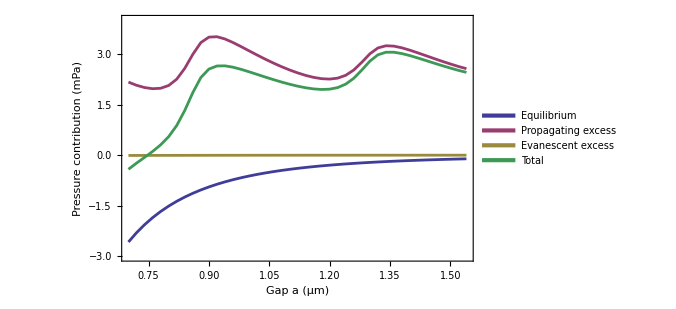

C:/Users/mrkho_000/Desktop/PRE_2026/New_optimization_version/figures_mathematica9_final/Clean_Figs/fig5_decomposition_final.pdf

```mathematica
(****************************************)
(*Figure 5: Decomposition*)
(****************************************)
decompRows={{0.7,-2.57417216821329,2.1650694512242095,-0.00917208624026328,-0.418274803229344},{0.72,-2.3001212283889,2.071087285895231,-0.00847804373361649,-0.23751198622729},{0.74,-2.06154158169111,2.0035158314659607,-0.00784721286181885,-0.0658729630869744},{0.7599999999999999,-1.85306528407714,1.96931608287124,-0.00727297749414364,0.10897782129995562},{0.7799999999999999,-1.67024863832102,1.9817617387221358,-0.00674948423187501,0.30476361616923126},{0.7999999999999999,-1.50939471896433,2.064252157791815,-0.00627155036671114,0.5485858884607695},{0.82,-1.36741333095534,2.2515333125173216,-0.00583458246384367,0.8782853990981281},{0.84,-1.24170983151374,2.5728259683535546,-0.00543450470352956,1.325681632136277},{0.86,-1.13009635447888,2.9882559675315403,-0.0050676960235264,1.853091917029127},{0.8799999999999999,-1.03072053208199,3.336585251376485,-0.00473093510138818,2.3011337841931017},{0.8999999999999999,-0.942007964943245,3.4975819702337487,-0.00442135226136585,2.551152653029137},{0.9199999999999999,-0.862615556101016,3.5094770818990866,-0.00413638746146548,2.642725138336605},{0.94,-0.791393476678718,3.4419805293488612,-0.00387375359745447,2.646713299072688},{0.96,-0.727354025161355,3.337060131554743,-0.00363140444359944,2.6060747019497876},{0.98,-0.669646019563654,3.216139406336272,-0.00340750662974082,2.543085880142877},{1,-0.617533651466082,3.0902632383160173,-0.00320041512836455,2.46952917172157},{1.02,-0.570378954593246,2.9653906156844614,-0.00300865179246179,2.392003009298753},{1.04,-0.527627214293238,2.844893293295228,-0.00283088654487235,2.3144351924571174},{1.06,-0.488794779837424,2.730765194709546,-0.00266592087268325,2.239304493999438},{1.08,-0.453458847799168,2.6244007578070727,-0.00251267332656449,2.1684292366813396},{1.1,-0.421248868589986,2.5270823008697825,-0.00237016676526222,2.1034632655145336},{1.1199999999999999,-0.391839294608754,2.440035891122895,-0.00223751712046667,2.0459590793936733},{1.1400000000000001,-0.364943441258571,2.3651484584141254,-0.00211392348755267,1.998091093668001},{1.16,-0.340308274265191,2.305587958863361,-0.00199865937384154,1.9632810252243282},{1.1800000000000002,-0.317709970566055,2.2658380099588427,-0.00189106495859065,1.9462369744341965},{1.2,-0.296950127289102,2.2541067315836,-0.00179054023836234,1.955366064056135},{1.22,-0.277852515371674,2.282056589686626,-0.00169653894818213,2.0025075353667696},{1.24,-0.260260292247876,2.3662710527546524,-0.00160856316334001,2.1044021973434357},{1.26,-0.244033602592528,2.5232713736381274,-0.00152615849914148,2.2777116125464576},{1.28,-0.229047508008406,2.7522952190435306,-0.00144890983665733,2.5217988011984667},{1.2999999999999998,-0.215190196299893,3.0020857459762436,-0.00137643751179462,2.7855191121645557},{1.32,-0.202361429001917,3.1770449840604513,-0.00130839391302264,2.9733751611455115},{1.3399999999999999,-0.190471192455951,3.241581298352037,-0.00124446044001617,3.0498656454560695},{1.36,-0.179438523206688,3.2305162877788476,-0.00118434478147536,3.0498934197906835},{1.38,-0.169190483043704,3.17913309587663,-0.00112777847557915,3.0088148343573455},{1.4,-0.159661262800983,3.108738270778002,-0.00107451472103757,2.948002493255981},{1.42,-0.150791397189889,3.0280972671480018,-0.00102432641062485,2.876281543547487},{1.44,-0.142527075588621,2.9452917661235163,-0.000977004362480922,2.8017876861724136},{1.46,-0.13481953593295,2.8613284621516173,-0.00093235572743398,2.7255765704912327},{1.48,-0.127624530722444,2.779829427431188,-0.000890202553182105,2.651314694155562},{1.5,-0.120901855733039,2.702376953024598,-0.00085038048842792,2.5806247168031304},{1.5199999999999998,-0.114614933359838,2.628338367261551,-0.000812737612032391,2.5129106962896794},{1.54,-0.108730443643621,2.562112159376919,-0.00077713337397921,2.4526045823593186}};

fig5Plot=With[{nLines=4},ListLinePlot[Table[decompRows[[All,{1,j}]],{j,2,5}],PlotStyle->Table[Directive[ColorData[1,i],Thickness[0.004]],{i,nLines}],Frame->True,Axes->False,FrameLabel->{Style["Gap \!\(\*StyleBox[\"a\",FontSlant->\"Italic\"]\) (μm)",FontFamily->"Times",FontSize->15],Style["Pressure contribution (mPa)",FontFamily->"Times",FontSize->15]},FrameTicksStyle->Directive[FontFamily->"Times",FontSize->15],PlotLegends->Placed[LineLegend[Table[Directive[ColorData[1,i],AbsoluteThickness[3]],{i,nLines}],{"Equilibrium","Propagating excess","Evanescent excess","Total"},(*V9 Solution:Controls vector length and line width precisely*)LegendMarkerSize->{25,1}],{0.8,0.2}],PlotRange->{-3,4},ImageSize->500,BaseStyle->{FontFamily->"Times",FontSize->15},PlotRangePadding->None]]

(****** Export *****)
Export["C:/Users/mrkho_000/Desktop/PRE_2026/New_optimization_version/figures_mathematica9_final/Clean_Figs/fig5_decomposition_final.pdf",fig5Plot]
```

## Figure 6

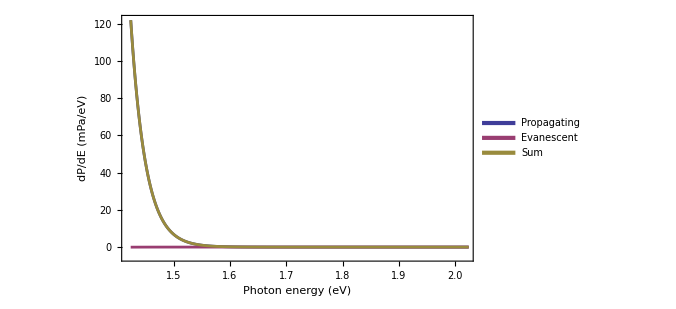

C:/Users/mrkho_000/Desktop/PRE_2026/New_optimization_version/figures_mathematica9_final/Clean_Figs/fig6_spectrum_optimum_final.pdf

```mathematica
(****************************************)
(*Figure 6: Spectrum at optimum*)
(****************************************)
spectrumRows={{1.424009606534469,2.46533381061297*10^-5,122.45046836313165,-0.0480115858436111,122.40245677728802},{1.4240506151046741,5.73856633972192*10^-5,122.26090718540843,-0.0479320737348059,122.21297511167361},{1.424124387965334,9.01601896224241*10^-5,121.9206358116491,-0.047789370271341,121.87284644137776},{1.424230933441018,0.000122929072021172,121.43088215131846,-0.0475840328209787,121.38329811849748},{1.4243702418940716,0.000155685364037891,120.79350877507514,-0.0473169041362928,120.74619187093884},{1.424542298577967,0.000188424893391399,120.01094115319145,-0.0469890824131861,119.96395207077826},{1.4247470848472363,0.000221143924771668,119.08614615317998,-0.046601912186154,119.03954424099383},{1.4249845783847,0.000253838828724185,118.02261158859942,-0.0461569752756647,117.97645461332375},{1.4252547532637527,0.000286506010330576,116.82432320577661,-0.0456560801714298,116.7786671256052},{1.4255575799710989,0.000319141889413748,115.49573873932178,-0.0451012496494471,115.45063748967235},{1.4258930254177196,0.000351742894111294,114.0417591555619,-0.0444947066782176,113.99726444888371},{1.4262610529458697,0.000384305458628499,112.46769732704418,-0.043838858765495,112.42385846827868},{1.426661622334703,0.000416826022497566,110.77924443083404,-0.0431362809490156,110.73610814988503},{1.427094689805497,0.000449301030440321,108.98243439010899,-0.0423896976643112,108.94004469244467},{1.4275602080268919,0.000481726932493265,107.08360669430185,-0.0416019637367753,107.04200473056505},{1.4280581261203218,0.000514100184256919,105.08936794170388,-0.0407760447480283,105.04859189695586},{1.4285883896657312,0.00054641724720552,103.00655245132539,-0.0399149970215702,102.96663745430382},{1.4291509407076182,0.000578674589030537,100.84218228901709,-0.0390219474623631,100.80316034155472},{1.42974571776143,0.000610868684000015,98.60342704687494,-0.0381000734711573,98.5653269734038},{1.4303726558203227,0.0006429960133264,96.29756370536852,-0.0371525831383488,96.26041112223017},{1.4310316863622932,0.000675053065541938,93.9319368948543,-0.0361826959047412,93.89575419894958},{1.4317227373576888,0.000707036336874752,91.51391985754883,-0.0351936238583064,91.47872623369052},{1.4324457332770897,0.000738942331629095,89.05087639310959,-0.0341885538172924,89.01668783929229},{1.4332005950995756,0.000770767562562196,86.55012405084254,-0.0331706303309854,86.51695342051156},{1.4339872403213683,0.000802508551263699,84.01889880990369,-0.0321429397104527,83.98675587019324},{1.4348055829648534,0.000834161828535501,81.46432146566076,-0.0311084951827306,81.43321297047802},{1.4356555335879826,0.000865723934769347,78.89336591621057,-0.0300702232434693,78.8632956929671},{1.4365369992940507,0.000897191420323507,76.31282951806655,-0.0290309512651381,76.28379856680142},{1.4374498837418515,0.00092856084590035,73.72930565451804,-0.0279933964006971,73.70131225811734},{1.438394087156209,0.000959828782920558,71.14915863445378,-0.0269601558063371,71.12219847864745},{1.4393695063388847,0.000990991813899152,68.57850101370445,-0.0259336981915816,68.55256731551287},{1.440376034679856,0.00102204653281767,66.02317340553077,-0.0249163566908708,65.99825704883989},{1.4414135621689708,0.00105298954549562,63.48872682197675,-0.0239103230377716,63.46481649893899},{1.4424819754079705,0.00108381746996301,60.98040756377467,-0.0229176430112661,60.9574899207634},{1.443581157622886,0.0011145269368294,58.503144653543465,-0.0219402131131797,58.48120444043028},{1.4447109886768,0.00114511458965095,56.06153978553395,-0.0209797784267498,56.04056000710721},{1.4458713450829777,0.00117557708529809,53.65985974527596,-0.0200379315985846,53.63982181367737},{1.447062100018365,0.0012059110943207,51.30203123441528,-0.0191161128798034,51.282915121535474},{1.4482831233374491,0.00123611330131253,48.99163801975951,-0.0182156111569378,48.97342240860257},{1.4495342815864825,0.00126618040527302,46.73192031102785,-0.0173375658991446,46.71458274512871},{1.4508154380180711,0.00129610911996672,44.52577625880058,-0.0164829699453746,44.509293288855204},{1.452126452606119,0.00132589617428558,42.37576545248115,-0.0156526730532867,42.360112779427865},{1.4534671820611331,0.00135553831260373,40.28411428743873,-0.0148473861307868,40.26926690130795},{1.4548374798458843,0.00138503229513418,38.25272306094228,-0.0140676860710547,38.23865537487122},{1.456237196191424,0.0014143748982831,36.283174648138825,-0.0133140211126854,36.269860627026134},{1.457666178113453,0.00144356291500224,34.37674460264784,-0.0125867166480414,34.3641578859998},{1.4591242694290425,0.00147259315513856,32.534412521932154,-0.0118859814049949,32.52252654052716},{1.4606113107737042,0.00150146244578404,30.75687451605333,-0.0112119139298626,30.745662602123467},{1.4621271396188085,0.00153016763162151,29.04455662001107,-0.0105645093024081,29.03399211070866},{1.463671590289348,0.00155870557527038,27.397628994395955,-0.00994366601724042,27.387685328378716},{1.4652444939820453,0.00158707315762905,25.816020765711688,-0.00934919296970113,25.806671572741983},{1.4668456787838045,0.00161526727821544,24.299435365124893,-0.00878081648833658,24.290654548636557},{1.4684749696904968,0.00164328485550653,22.84736623115176,-0.00823818736023941,22.839128043791522},{1.470132188626092,0.00167112282727532,21.45911274680721,-0.00772088779984795,21.451391859007362},{1.4718171544621192,0.00169877815092446,20.13379628499721,-0.0072284383161844,20.126567846681024},{1.4735296830374642,0.00172624780381962,18.870376238343276,-0.00676030443791388,18.86361593390536},{1.4752695871784978,0.00175352878361979,17.667665913202118,-0.00631590326000345,17.66135000994212},{1.4770366767195329,0.00178061810860542,16.524348174440203,-0.00589460978009656,16.518453564660103},{1.4788307585236096,0.0018075128180041,15.438990738859895,-0.00549576299696808,15.433494975862928},{1.4806516365036044,0.00183420997231346,14.410061030685947,-0.00511867174755545,14.40494235893839},{1.4824991116436603,0.00186070665362508,13.435940529977204,-0.00476262026304763,13.431177909714156},{1.4843729820209417,0.0018869999659396,12.514938560757365,-0.00442687342832869,12.510511687329036},{1.4862730428277002,0.00191308703548666,11.64530547681865,-0.00411068173270767,11.641194795085942},{1.4881990863936625,0.00193896501103711,10.825245208025624,-0.0038132859032876,10.821431922122336},{1.4901509022087258,0.00196463106421431,10.052927129909694,-0.00353392121554174,10.049393208694154},{1.492128276945968,0.00199008238980509,9.326497218208525,-0.003271821478645,9.32322539672988},{1.4941309944849617,0.00201531620606469,8.644088452565526,-0.00302622269586,8.641062229869666},{1.4961588359353961,0.002040329755022,8.00383044308451,-0.00279636640278527,8.001034076681723},{1.4982115796610018,0.00206512030277936,7.403858269609083,-0.00258150268854324,7.40127676692054},{1.500289001303773,0.00208968513981362,6.842320542351106,-0.0023808929070121,6.839939649444094},{1.5023908738084921,0.00211402158126988,6.317386707631263,-0.00219381208699284,6.31519289554427},{1.5045169674475425,0.00213812696725702,5.827253628910898,-0.0020195510517573,5.825234077859141},{1.50666704984602,0.00216199866313678,5.37015146992577,-0.00185741825974437,5.368294051666027},{1.5088408860071283,0.0021856340598136,4.944348897614687,-0.00170674137927596,4.9426421562354115},{1.5110382383378658,0.00220903057401695,4.548157614899567,-0.0015668686110533,4.546590746288513},{1.5132588666749913,0.00223218564858707,4.1799362338193395,-0.0014371697728834,4.1784990640464565},{1.5155025283112749,0.00225509675275145,3.8380935100229716,-0.00131703716158385,3.836776472861388},{1.5177689780220236,0.00227776138240317,3.5210909760427063,-0.00120588620733555,3.5198850898353706},{1.5200579680918853,0.00230017706037431,3.22744502485592,-0.00110315593590996,3.22634186892001},{1.522369248341921,0.00232234133670684,2.9557284994903266,-0.00100830925420404,2.954720190236123},{1.5247025661569507,0.00234425178891905,2.704571836726592,-0.000920833074386245,2.703651003652206},{1.5270576665131617,0.00236590602227239,2.472663798213452,-0.000840238291705473,2.4718235599217464},{1.5294342920059831,0.00238730167003171,2.258751809675956,-0.000766059630654992,2.2579857500453007},{1.5318321828782189,0.00240843639372401,2.061641926189228,-0.000697855373730124,2.060944070815498},{1.5342510770484377,0.0024293078833953,1.8801984502101012,-0.000635206986485147,1.8795632432236162},{1.5366907101396188,0.00244991385786179,1.7133432432479225,-0.000577718651994611,1.7127655245959277},{1.5391508155080467,0.00247025206495934,1.5600547819688717,-0.000525016727170242,1.5595297652417015},{1.5416311242724536,0.00249032028179008,1.4193670079957799,-0.000476749132688217,1.4188902588630916},{1.5441313653434108,0.00251011631496574,1.2903680079422883,-0.00043258468755465,1.2899354232547338},{1.546651265452953,0.00252963800084517,1.1721985438799296,-0.000392212398590134,1.1718063314813394},{1.5491905491844487,0.00254888320577455,1.0640504442753305,-0.000355340714355807,1.0636951035609747},{1.5517489390027015,0.00256784982631718,0.9651648668905229,-0.000321696752283941,0.964843170138239},{1.554326155284284,0.00258653578948506,0.8748304556812099,-0.000291025507021785,0.874539430174188},{1.5569219163480994,0.00260493905296516,0.7923814246983255,-0.00026308904725609,0.7921183356510695},{1.5595359384861676,0.00262305760534228,0.717195604628897,-0.000237665707563199,0.7169579389213339},{1.5621679359946357,0.00264088946631937,0.6486924791490327,-0.000214549281130688,0.648477929867902},{1.5648176212050022,0.00265843268693435,0.5863312238121583,-0.000193548218526069,0.5861376755936322},{1.567484704515559,0.00267568534977137,0.5296087488923205,-0.000174484837048781,0.5294342640552717},{1.5701688944230445,0.0026926455691725,0.47805774596792255,-0.000157194544597037,0.47790055142332555},{1.5728698975545032,0.0027093114914429,0.4312447454813955,-0.000141525081412611,0.43110322039998294},{1.5755874186993504,0.00272568129505258,0.3887682021513579,-0.000127335782535793,0.38864086636882206},{1.5783211608416383,0.0027417531908375,0.3502566289469665,-0.000114496863310465,0.350142132083656},{1.581070825192518,0.00275752542219268,0.31536679500465253,-0.000102888729825619,0.3152639062748269},{1.5838361112228971,0.00277299626526679,0.2837819918741901,-9.24013157645013*10^-5,0.2836895905584256},{1.586616716696286,0.00278816402914804,0.2552103632989202,-8.29334467554153*10^-5,0.2551274298521648},{1.5894123377018305,0.00280302705605109,0.22938329207625363,-7.43922329778757*10^-5,0.2293088998432758},{1.5922226686875303,0.00281758372149665,0.20605384324874507,-6.66924904732458*10^-5,0.20598715075827184},{1.5950474024936325,0.00283183243449028,0.18499527049393066,-5.97561913385692*10^-5,0.18493551430259209},{1.5978862303862054,0.00284577163769511,0.16599959582235088,-5.35119427444062*10^-5,0.1659460838796065},{1.6007388420908797,0.00285939980760337,0.14887626906136955,-4.78944945102658*10^-5,0.1488283745668593},{1.6036049258267624,0.00287271545470142,0.1334509058822416,-4.28442747927515*10^-5,0.13340806160744884},{1.6064841683405124,0.00288571712363388,0.11956409694032649,-0.000038306953289844,0.11952578998703664},{1.6093762549405788,0.0028984033933617,0.10707028011151623,-3.42330312377646*10^-5,0.10703604708027846},{1.612280869531594,0.0029107728773184,0.0958366723805809,-3.05774573726093*10^-5,0.0958060949232083},{1.6151976946489244,0.0029228242235608,0.0857422634495356,-0.000027299268945379,0.0857149641805902},{1.6181264114933658,0.00293455611491695,0.0766768751793055,-2.43612568142361*10^-5,0.0766525139224913},{1.6210666999659882,0.0029459672691309,0.0685402882741815,-2.17296535898386*10^-5,0.0685185586205916},{1.6240182387031221,0.00295705643900159,0.0612414325558803,-1.93738437766823*10^-5,0.0612220587121036},{1.6269807051114815,0.00296782241251971,0.0546976336304861,-1.72660948337381*10^-5,0.0546803675356524},{1.629953775403422,0.00297826401300081,0.048833909102523665,-1.53813080696949*10^-5,0.0488185277944539},{1.632937124632331,0.00298838009921263,0.0435823109829994,-1.36967882902661*10^-5,0.0435686141947091},{1.6359304267281423,0.00299816956550069,0.0388813145462359,-1.21920311258832*10^-5,0.0388691225151101},{1.638933354532975,0.00300763134190984,0.034675254878837505,-1.08485269863241*10^-5,0.0346644063518511},{1.6419455798368896,0.00301676439429936,0.0309138103598183,-9.64958061326001*10^-6,0.030904160779205127},{1.6449667734137623,0.00302556772445695,0.0275515292377601,-8.58014523118638*10^-6,0.027542949092528933},{1.6479966050572665,0.00303404037020843,0.0245473937612291,-7.62667033079343*10^-6,0.0245397670908983},{1.6510347436169641,0.00304218140552209,0.0218644170800714,-6.77696215558743*10^-6,0.021857640117915907},{1.6540808570344985,0.0030499899406099,0.019469270543249505,-6.02005600173166*10^-6,0.0194632504872477},{1.657134612379888,0.00305746512202515,0.017331941138945622,-5.34609948190768*10^-6,0.017326595039463714},{1.6601956758879146,0.00306460613275574,0.015425419172395434,-4.74624594589537*10^-6,0.015420672926449538},{1.6632637129946017,0.00307141219231285,0.013725414916356262,-4.21255729298681*10^-6,0.013721202359063274},{1.666338388373782,0.00307788255681719,0.012210101247606044,-3.73791545382392*10^-6,0.012206363332152219},{1.669419365973747,0.00308401651907995,0.010859878595523443,-3.31594186138656*10^-6,0.010856562653662059},{1.6725063090539778,0.00308981340867908,0.00965715927415576,-2.94092427232056*10^-6,0.00965421834988344},{1.675598880221947,0.00309527259203419,0.00858616975868112,-2.60775034030989*10^-6,0.00858356200834081},{1.6786967414699971,0.00310039347247473,0.00763277059628349,-2.31184738253812*10^-6,0.00763045874890095},{1.681799554212282,0.003105175490306,0.00678429371686822,-2.04912781827366*10^-6,0.00678224458904995},{1.6849069793217744,0.00310961812286904,0.00602939609564103,-1.81593979511098*10^-6,0.00602758015584592},{1.68801867716733,0.00311372088459943,0.00535792782053318,-1.60902255330726*10^-6,0.00535631879797987},{1.6911343076508096,0.00311748332707867,0.00476081237541629,-1.4254661118977*10^-6,0.00475938690930439},{1.6942535302442492,0.00312090503908488,0.00422993748695864,-1.26267489181281*10^-6,0.00422867481206683},{1.6973760040270798,0.00312398564663568,0.00375805573086027,-1.11833492103605*10^-6,0.00375693739593924},{1.7005013877233877,0.00312672481303161,0.00333869465953924,-9.90384294933474*10^-7,0.00333770427524431},{1.703629339739216,0.00312912223889103,0.00296607621107545,-8.76986591273866*10^-7,0.00296519922448417},{1.7067595181998987,0.00313117766218284,0.00263504473209093,-7.76506964172741*10^-7,0.00263426822512676},{1.7098915809874269,0.00313289085825664,0.00234100250544164,-6.87490664277215*10^-7,0.00234031501477736},{1.7130251857778414,0.00313426163986551,0.0020798515784545,-6.08643754015825*10^-7,0.00207924293470049},{1.7161599900786466,0.00313528985718778,0.00184794099389984,-5.38815806725854*10^-7,0.00184740217809311},{1.7192956512662452,0.0031359753978428,0.00164201898215589,-4.76984397006249*10^-7,0.00164154199775888},{1.7224318266233847,0.00313631818690296,0.00145918996487822,-4.22241206795807*10^-7,0.00145876772367142},{1.7255681733766153,0.00313631818690305,0.00129687621617508,-3.73779587515199*10^-7,0.00129650243658757},{1.7287043487337548,0.00313597539784284,0.00115278382196901,-3.30883433211347*10^-7,0.0011524529385358},{1.7318400099213533,0.00313528985718787,0.0010248723343953,-2.92917488073843*10^-7,0.00102457941690723},{1.7349748142221586,0.00313426163986566,0.00091132753814107,-2.5931882621336*10^-7,0.000911068219314857},{1.7381084190125728,0.00313289085825673,0.000810537152329461,-2.2958709909451*10^-7,0.000810307565230367},{1.7412404818001013,0.00313117766218302,0.000721068465721072,-2.03278617126081*10^-7,0.000720865187103946},{1.7443706602607838,0.00312912223889097,0.00064164843193868,-1.80000157492665*10^-7,0.000641468431781187},{1.747498612276612,0.00312672481303175,0.000571146003215274,-1.59403320096824*10^-7,0.000570986599895177},{1.7506239959729202,0.00312398564663582,0.000508556517152893,-1.41179504118701*10^-7,0.000508415337648774},{1.7537464697557505,0.00312090503908476,0.00045298787011562,-1.25055443089642*10^-7,0.000452862814672531},{1.7568656923491905,0.00311748332707871,0.000403648174439933,-1.10789247343962*10^-7,0.000403537385192589},{1.75998132283267,0.00311372088459945,0.000359834637325149,-9.81669220717404*10^-8,0.000359736470403077},{1.7630930206782256,0.00310961812286908,0.000320923461393226,-8.69993854692441*10^-8,0.000320836462007757},{1.7662004457877178,0.00310517549030604,0.00028636046409669,-7.71202954381598*10^-8,0.000286283343801252},{1.7693032585300028,0.00310039347247482,0.000255649519374967,-6.83888979189362*10^-8,0.000255581130477048},{1.7724011197780527,0.00309527259203437,0.000228373294362584,-6.07011972336313*10^-8,0.00022831259316535},{1.7754936909460222,0.00308981340867906,0.000204150225872989,-5.38463988575293*10^-8,0.000204096379474131},{1.7785806340262527,0.00308401651907994,0.000182620768551246,-4.77708310485324*10^-8,0.000182572997720198},{1.781661611626218,0.00307788255681727,0.000163480977871712,-4.23884328377691*10^-8,0.000163438589438874},{1.7847362870053984,0.0030714121923129,0.000146461288128904,-3.76205492146104*10^-8,0.00014642366757969},{1.7878043241120853,0.00306460613275572,0.000131322571045491,-3.33969068608572*10^-8,0.00013128917413863},{1.7908653876201117,0.00305746512202519,0.000117852607341985,-2.96550695147642*10^-8,0.000117822952272471},{1.7939191429655015,0.00304998994060988,0.000105862972512942,-2.63396824725579*10^-8,0.00010583663283047},{1.7969652563830358,0.00304218140552201,9.51863050848364*10^-5,-2.34017199212694*10^-8,9.51629033649151*10^-5},{1.8000033949427332,0.00303404037020845,8.56739065146572*10^-5,-2.07977860073177*10^-8,8.56531087286499*10^-5},{1.8030332265862374,0.00302556772445701,7.71936166504047*10^-5,-1.84894813951002*10^-8,7.71751271690096*10^-5},{1.8060544201631101,0.00301676439429931,6.96279205074358*10^-5,-1.64428352191283*10^-8,6.96114776722167*10^-5},{1.809066645467025,0.00300763134190986,6.28722630722954*10^-5,-1.46277983885969*10^-8,6.28576352739068*10^-5},{1.8120695732718577,0.00299816956550087,5.68335665478501*10^-5,-1.30177929709147*10^-8,5.68205487548792*10^-5},{1.815062875367669,0.0029883800992126,5.14289512605812*10^-5,-1.15893121822016*10^-8,0.000051417361948399},{1.818046224596578,0.00297826401300061,4.65846572717473*10^-5,-1.03215657282624*10^-8,0.000046574335706019},{1.8210192948885184,0.00296782241251967,4.22351526588174*10^-5,-9.19616561694383*10^-9,4.22259564932005*10^-5},{1.8239817612968776,0.00295705643900156,3.83224009681903*10^-5,-8.19684799237492*10^-9,0.000038314204120198},{1.8269333000340118,0.00294596726913096,3.47952483860032*10^-5,-7.30922697377652*10^-9,3.47879391590294*10^-5},{1.8298735885066342,0.00293455611491698,3.16088842129545*10^-5,-6.52057689378657*10^-9,3.16023636360607*10^-5},{1.8328023053510756,0.00292282422356078,2.87243287826739*10^-5,-5.81963971393838*10^-9,0.00002871850914296},{1.8357191304684057,0.00291077287731841,2.61079116995099*10^-5,-5.19645474471491*10^-9,2.61027152447652*10^-5},{1.8386237450594212,0.00289840339336172,2.37307187760553*10^-5,-4.64220811429078*10^-9,0.000023726076567941},{1.8415158316594873,0.00288571712363378,2.15680051335889*10^-5,-4.14909971506114*10^-9,2.15638560338738*10^-5},{1.8443950741732376,0.00287271545470137,1.95985900853846*10^-5,-3.71022561243422*10^-9,1.95948798597722*10^-5},{1.8472611579091203,0.00285939980760327,1.78042618717499*10^-5,-3.31947412854957*10^-9,1.78009423976213*10^-5},{1.8501137696137946,0.0028457716376951,0.00001616922387908,-2.97143401702019*10^-9,0.000016166252445063},{1.8529525975063672,0.00283183243449027,1.46796087301233*10^-5,-2.66131332587907*10^-9,1.46769474167974*10^-5},{1.8557773313124697,0.00281758372149678,1.33230758108882*10^-5,-2.38486770688093*10^-9,1.33206909431813*10^-5},{1.8585876622981694,0.00280302705605105,0.000012088495838084,-2.13833707226128*10^-9,1.20863575010117*10^-5},{1.861383283303714,0.00278816402914807,1.09657163558581*10^-5,-1.9183896268899*10^-9,1.09637979662312*10^-5},{1.8641638887771026,0.00277299626526669,9.945395929304776*10^-6,-1.72207241621788*10^-9,9.943673856888559*10^-6},{1.8669291748074819,0.00275752542219265,9.018892060372095*10^-6,-1.54676763006994*10^-9,9.017345292742024*10^-6},{1.8696788391583616,0.00274175319083734,8.178187700057618*10^-6,-1.39015399059308*10^-9,8.176797546067026*10^-6},{1.8724125813006496,0.00272568129505261,7.415842894300689*10^-6,-1.25017263080266*10^-9,7.4145927216698865*10^-6},{1.8751301024454967,0.00270931149144275,6.724960879729843*10^-6,-1.12499693930608*10^-9,6.723835882790536*10^-6},{1.8778311055769554,0.00269264556917257,6.099161131613806*10^-6,-1.01300590794074*10^-9,6.098148125705865*10^-6},{1.8805152954844409,0.00267568534977141,5.532554811624616*10^-6,-9.12760573145686*10^-10,5.531642051051471*10^-6},{1.8831823787949977,0.00265843268693427,5.019720345684659*10^-6,-8.22983189695732*10^-10,5.018897362494964*10^-6},{1.885832064005364,0.00264088946631951,4.555678363922188*10^-6,-7.42538817683767*10^-10,4.554935825104505*10^-6},{1.8884640615138322,0.00262305760534237,4.135866060132688*10^-6,-6.70419040973808*10^-10,4.135195641091715*10^-6},{1.8910780836519006,0.00260493905296514,3.7561113628442206*10^-6,-6.05727568333592*10^-10,3.7555056352758868*10^-6},{1.8936738447157158,0.00258653578948515,3.4126073316645754*10^-6,-5.4766749759032*10^-10,3.4120596641669846*10^-6},{1.8962510609972982,0.00256784982631728,3.1018870543368825*10^-6,-4.95530048883468*10^-10,3.1013915242879995*10^-6},{1.898809450815551,0.00254888320577461,2.8207991558970597*10^-6,-4.4868459580827*10^-10,2.820350471301251*10^-6},{1.901348734547047,0.00252963800084516,2.5664839397706392*10^-6,-4.06569843302584*10^-10,2.5660773699273366*10^-6},{1.903868634656589,0.00251011631496544,2.3363501951497207*10^-6,-3.68686018837974*10^-10,2.3359815091308826*10^-6},{1.906368875727546,0.00249032028179007,2.128052789564487*10^-6,-3.34587959106863*10^-10,2.12771820160538*10^-6},{1.9088491844919535,0.00247025206495924,1.93947124873706*10^-6,-3.03878988194715*10^-10,1.939167369748865*10^-6},{1.9113092898603812,0.00244991385786179,1.7686895506289308*10^-6,-2.7620549540289*10^-10,1.7684133451335279*10^-6},{1.9137489229515623,0.00242930788339533,1.6139773148222566*10^-6,-2.51252131634891*10^-10,1.613726062690622*10^-6},{1.916167817121781,0.00240843639372408,1.473772479300828*10^-6,-2.2873755274292*10^-10,1.4735437417480852*10^-6},{1.9185657079940166,0.00238730167003149,1.3466654638371023*10^-6,-2.0841064660171*10^-10,1.3464570531905006*10^-6},{1.9209423334868383,0.00236590602227229,1.2313847494561453*10^-6,-1.90047188063119*10^-10,1.2311947022680821*10^-6},{1.9232974338430493,0.00234425178891901,1.1267837637532298*10^-6,-1.73446872463653*10^-10,1.126610316880766*10^-6},{1.9256307516580788,0.00232234133670677,1.0318289466850173*10^-6,-1.58430684109935*10^-10,1.0316705160009074*10^-6},{1.9279420319081146,0.00230017706037443,9.455888733921377*10^-7,-1.44838561244454*10^-10,9.454440348308932*10^-7},{1.9302310219779761,0.0022777613824032,8.672243246889113*10^-7,-1.32527323474942*10^-10,8.670917973654364*10^-7},{1.9324974716887249,0.00225509675275127,7.95979217931883*10^-7,-1.21368831606032*10^-10,7.958578491002769*10^-7},{1.9347411333250086,0.00223218564858697,7.311723351605151*10^-7,-1.11248353303052*10^-10,7.310610868072122*10^-7},{1.9369617616621342,0.00220903057401702,6.721898045435519*10^-7,-1.02063111099821*10^-10,6.72087741432452*10^-7},{1.9391591139928717,0.00218563405981354,6.184782999801075*10^-7,-9.37209919831843*10^-11,6.183845789881243*10^-7},{1.94133295015398,0.00216199866313688,5.69538921535492*10^-7,-8.61394001894187*10^-11,5.694527821353025*10^-7},{1.9434830325524572,0.00213812696725698,5.249217102636758*10^-7,-7.9244236969002*10^-11,5.248424660267068*10^-7},{1.9456091261915078,0.00211402158126986,4.842207410447886*10^-7,-7.29689929496781*10^-11,4.84147772051839*10^-7},{1.9477109986962269,0.00208968513981352,4.4706973138444467*10^-7,-6.72539403824895*10^-11,4.470024774440622*10^-7},{1.9497884203389984,0.00206512030277945,4.131381046396037*10^-7,-6.20454140171665*10^-11,4.130760592255865*10^-7},{1.9518411640646038,0.00204032975502201,3.8212745181180846*10^-7,-5.7295170644729*10^-11,3.820701566411637*10^-7},{1.9538690055150383,0.00201531620606486,3.5376834431408866*10^-7,-5.29598184863289*10^-11,3.537153844956023*10^-7},{1.955871723054032,0.00199008238980511,3.278174585032326*10^-7,-4.90003086159207*10^-11,3.2776845819461667*10^-7},{1.957849097791274,0.00196463106421431,3.040549798202112*10^-7,-4.5381481495877*10^-11,3.0400959833871535*10^-7},{1.9598009136063375,0.00193896501103702,2.8228225971596*10^-7,-4.20716624928551*10^-11,2.822401880534672*10^-7},{1.9617269571722997,0.00191308703548677,2.623197024097759*10^-7,-3.90423009382253*10^-11,2.622806601088377*10^-7},{1.9636270179790583,0.00188699996593975,2.440048613360834*10^-7,-3.62676479138216*10^-11,2.4396859368816965*10^-7},{1.9655008883563394,0.00186070665362502,2.271907271725623*10^-7,-3.37244684891349*10^-11,2.2715700270407317*10^-7},{1.9673483634963957,0.0018342099723135,2.1174419076143018*10^-7,-3.1391784618619*10^-11,2.1171279897681157*10^-7},{1.9691692414763904,0.00180751281800378,1.9754466515233262*10^-7,-2.92506453348526*10^-11,1.9751541450699776*10^-7},{1.970963323280467,0.00178061810860536,1.8448285157907748*10^-7,-2.72839212513708*10^-11,1.8445556765782613*10^-7},{1.9727304128215022,0.00175352878361982,1.7245963466527836*10^-7,-2.54761207237506*10^-11,1.724341585445546*10^-7},{1.9744703169625357,0.0017262478038196,1.6138509276834883*10^-7,-2.3813225314028*10^-11,1.613612795430348*10^-7},{1.9761828455378807,0.0016987781509244,1.511776102707903*10^-7,-2.22825424661966*10^-11,1.511553277283241*10^-7},{1.9778678113739079,0.00167112282727537,1.4176307984098404*10^-7,-2.08725735333047*10^-11,1.4174220726745074*10^-7},{1.979525030309503,0.00164328485550669,1.33074184124802*10^-7,-1.95728955029867*10^-11,1.33054611229299*10^-7},{1.9811543212161955,0.00161526727821542,1.25049747839751*10^-7,-1.83740549511926*10^-11,1.2503137378479983*10^-7},{1.9827555060179545,0.00158707315762904,1.1763415266524368*10^-7,-1.72674729161234*10^-11,1.1761688519232757*10^-7},{1.9843284097106522,0.0015587055752704,1.1077680853865058*10^-7,-1.62453595283022*10^-11,1.107605631791223*10^-7},{1.9858728603811915,0.00153016763162147,1.0443167592392421*10^-7,-1.53006373604393*10^-11,1.0441637528656376*10^-7},{1.9873886892262957,0.00150146244578387,9.855683432485685*10^-8,-1.44268725741257*10^-11,9.854240745228272*10^-8},{1.9888757305709575,0.00147259315513851,9.311409281658576*10^-8,-1.3618213041064*10^-11,9.310047460354469*10^-8},{1.990333821886547,0.00144356291500221,8.806863873151936*10^-8,-1.28693327059683*10^-11,8.805576939881339*10^-8},{1.9917628038085762,0.00141437489828321,8.338872092062024*10^-8,-1.21753815377187*10^-11,8.337654553908252*10^-8},{1.9931625201541159,0.0013850322951343,7.904536426317127*10^-8,-1.1531940485977*10^-11,7.90338323226853*10^-8},{1.994532817938867,0.00135553831260383,7.5012112343699*10^-8,-1.09349809232593*10^-11,7.500117736277575*10^-8},{1.995873547393881,0.0013258961742857,7.126479546309214*10^-8,-1.03808281083059*10^-11,7.125441463498382*10^-8},{1.9971845619819288,0.00129610911996681,6.778132140066803*10^-8,-9.8661282562804*10^-12,6.777145527241175*10^-8},{1.9984657184135175,0.00126618040527282,6.454148658901281*10^-8,-9.38781884555017*10^-12,6.453209877016727*10^-8},{1.999716876662551,0.00123611330131269,6.152680559729721*10^-8,-8.94310183017716*10^-12,6.151786249546702*10^-8},{2.000937899981635,0.0012059110943208,5.872035703689787*10^-8,-8.52941946232162*10^-12,5.871182761743555*10^-8},{2.0021286549170223,0.00117557708529798,5.6106644203199955*10^-8,-8.14443246000732*10^-12,5.609849977073994*10^-8},{2.0032890113232003,0.00114511458965095,5.367146894914247*10^-8,-7.78600028355304*10^-12,5.366368294885893*10^-8},{2.004418842377114,0.00111452693682954,5.140181745004685*10^-8,-7.4521633088131*10^-12,5.139436528673804*10^-8},{2.0055180245920297,0.00108381746996322,4.928575666664098*10^-8,-7.14112670752456*10^-12,4.927861553993345*10^-8},{2.0065864378310296,0.00105298954549557,4.731234044510181*10^-8,-6.85124586483403*10^-12,4.730548919923698*10^-8},{2.007623965320144,0.0010220465328175,4.547152431033048*10^-8,-6.58101318172814*10^-12,4.5464943297148755*10^-8},{2.0086304936611157,0.000990991813899225,4.3754088112523117*10^-8,-6.32904612585823*10^-12,4.374775906639726*10^-8},{2.009605912843791,0.000959828782920605,4.21515657784095*10^-8,-6.0940764083415*10^-12,4.214547170200116*10^-8},{2.0105501162581487,0.000928560845900235,4.065618149829681*10^-8,-5.87494017670832*10^-12,4.0650306558120096*10^-8},{2.0114630007059495,0.000897191420323537,3.926079174969036*10^-8,-5.67056912543836*10^-12,3.9255121180564924*10^-8},{2.0123444664120176,0.000865723934769365,3.795883261881937*10^-8,-5.47998243559669*10^-12,3.795335263638377*10^-8},{2.013194417035147,0.00083416182853561,3.674427193446669*10^-8,-5.30227946411185*10^-12,3.6738969655002573*10^-8},{2.0140127596786317,0.000802508551263753,3.561156577510096*10^-8,-5.13663311131378*10^-12,3.5606429141989644*10^-8},{2.0147994049004243,0.000770767562562292,3.4555618951711495*10^-8,-4.98228380259475*10^-12,3.45506366679089*10^-8},{2.0155542667229103,0.000738942331629427,3.357174910580506*10^-8,-4.83853402655004*10^-12,3.356691057177851*10^-8},{2.016277262642311,0.00070703633687504,3.265565409549155*10^-8,-4.70474337778086*10^-12,3.2650949352113766*10^-8},{2.016968313637707,0.00067505306554178,3.180338237307144*10^-8,-4.58032405777538*10^-12,3.179880204901367*10^-8},{2.0176273441796777,0.000642996013326242,3.101130608540196*10^-8,-4.46473679198422*10^-12,3.100684134860998*10^-8},{2.01825428223857,0.000610868683999898,3.0276096653873215*10^-8,-4.35748712543184*10^-12,3.027173916674779*10^-8},{2.0188490592923816,0.000578674589030524,2.959470261430909*10^-8,-4.25812206301149*10^-12,2.9590444492246075*10^-8},{2.0194116103342687,0.000546417247205333,2.896432951862956*10^-8,-4.16622702403687*10^-12,2.8960163291605526*10^-8},{2.019941873879678,0.000514100184256702,2.8382421719835215*10^-8,-4.08142308371376*10^-12,2.8378340296751498*10^-8},{2.020439791973108,0.000481726932493233,2.7846645879904946*10^-8,-4.00336447698497*10^-12,2.784264251542796*10^-8},{2.020905310194503,0.000449301030440266,2.73548760566485*10^-8,-3.93173634272459*10^-12,2.7350944320305777*10^-8},{2.021338377665297,0.000416826022497471,2.6905180240531287*10^-8,-3.86625268853997*10^-12,2.690131398784275*10^-8},{2.0217389470541303,0.000384305458628403,2.6495808226122122*10^-8,-3.8066545585114*10^-12,2.6492001571563612*10^-8},{2.0221069745822806,0.000351742894111382,2.6125180715204397*10^-8,-3.75270838807968*10^-12,2.612142800681632*10^-8},{2.022442420028901,0.000319141889413913,2.5791879559848542*10^-8,-3.70420453200209*10^-12,2.5788175355316542*10^-8},{2.0227452467362474,0.000286506010330575,2.549463906396257*10^-8,-3.66095595285194*10^-12,2.549097810800972*10^-8},{2.0230154216153,0.000253838828724258,2.5232338271057656*10^-8,-3.62279705894472*10^-12,2.522871547399871*10^-8},{2.0232529151527636,0.000221143924771758,2.5003994174066394*10^-8,-3.58958268181637*10^-12,2.500040459138458*10^-8},{2.023457701422033,0.000188424893391574,2.480875578953157*10^-8,-3.56118718438395*10^-12,2.4805194602347183*10^-8},{2.0236297581059284,0.000155685364037827,2.464589904100381*10^-8,-3.53750369134629*10^-12,2.464236153731246*10^-8},{2.023769066558982,0.000122929072021072,2.451482238477838*10^-8,-3.51844343173832*10^-12,2.451130394134664*10^-8},{2.023875612034666,9.01601896225303*10^-5,2.44150430267652*10^-8,-3.50393517134706*10^-12,2.441153909159385*10^-8},{2.023949384895326,5.73856633971946*10^-5,2.434619294143897*10^-8,-3.49392462001519*10^-12,2.4342699016818953*10^-8},{2.0239903934655312,2.46533381060996*10^-5,2.4308004754939892*10^-8,-3.48837236876032*10^-12,2.4304516382571132*10^-8}};
fig6Plot=With[{nLines=3},ListLinePlot[{spectrumRows[[All,{1,3}]],spectrumRows[[All,{1,4}]],spectrumRows[[All,{1,5}]]},PlotStyle->Thickness[0.004],
Frame->True,Axes->False,FrameLabel -> {
 Style[
  "Photon energy (eV)",
  FontFamily -> "Times", FontSize -> 15
 ],
 Style[
  "dP/dE (mPa/eV)",
  FontFamily -> "Times", FontSize -> 15
 ]
},
FrameTicksStyle -> Directive[FontFamily -> "Times", FontSize -> 15],
PlotLegends->Placed[LineLegend[Table[Directive[ColorData[1,i],AbsoluteThickness[3]],{i,nLines}],{"Propagating","Evanescent","Sum"},LegendMarkerSize->{25,1}],{0.85,0.8}],PlotRange->{{1.42,2.02},{-5,122}},ImageSize->500,
BaseStyle->{FontFamily->"Times",FontSize->15},PlotRangePadding->None]]

(***** Export *****)
Export["C:/Users/mrkho_000/Desktop/PRE_2026/New_optimization_version/figures_mathematica9_final/Clean_Figs/fig6_spectrum_optimum_final.pdf",fig6Plot]
```

## Figure 7

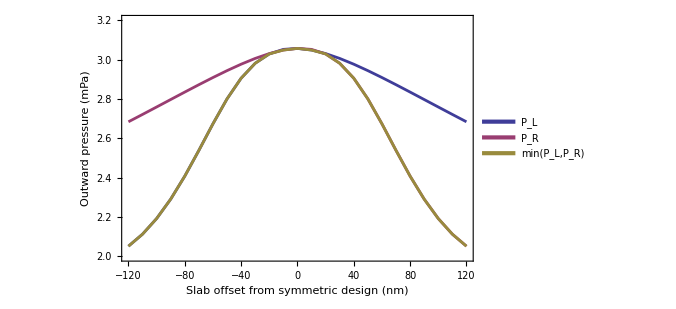

C:/Users/mrkho_000/Desktop/PRE_2026/New_optimization_version/figures_mathematica9_final/Clean_Figs/fig7_asymmetry_final.pdf

```mathematica
(****************************************)
(*Figure 7: Asymmetry diagnostic*)
(****************************************)
asymRows={{-120,2.0517763402804583,2.683743889532956,2.0517763402804583},{-110,2.112818978373327,2.721111439798737,2.112818978373327},{-100,2.1921335445206624,2.758892321208463,2.1921335445206624},{-90,2.290756358921524,2.796852615060471,2.290756358921524},{-80,2.40765094144414,2.834708570130128,2.40765094144414},{-70,2.538275985873468,2.8721064225724584,2.538275985873468},{-60,2.6734389567770074,2.908594844133915,2.6734389567770074},{-50,2.8000109944316507,2.9435863721056155,2.8000109944316507},{-40,2.905006146312944,2.9763023571075067,2.905006146312944},{-30,2.9810891900794334,3.005693341644069,2.9810891900794334},{-20,3.0283890300133094,3.0303234655958344,3.0283890300133094},{-10,3.05163002098684,3.048204986551445,3.048204986551445},{0,3.056573755123807,3.056573755123807,3.056573755123807},{9.999999999999984,3.048204986551445,3.05163002098684,3.048204986551445},{19.999999999999993,3.0303234655958344,3.0283890300133094,3.0283890300133094},{29.99999999999998,3.005693341644069,2.9810891900794334,2.9810891900794334},{39.999999999999986,2.9763023571075067,2.905006146312944,2.905006146312944},{50,2.9435863721056155,2.8000109944316507,2.8000109944316507},{59.99999999999998,2.908594844133915,2.6734389567770074,2.6734389567770074},{69.99999999999999,2.8721064225724584,2.538275985873468,2.538275985873468},{79.99999999999997,2.834708570130128,2.40765094144414,2.40765094144414},{89.99999999999999,2.796852615060471,2.290756358921524,2.290756358921524},{100,2.7588923212084637,2.1921335445206624,2.1921335445206624},{109.99999999999999,2.721111439798737,2.112818978373327,2.112818978373327},{120.00000000000001,2.683743889532956,2.0517763402804583,2.0517763402804583}};
fig7Plot=With[{nLines=3},ListLinePlot[{asymRows[[All,{1,2}]],asymRows[[All,{1,3}]],asymRows[[All,{1,4}]]},PlotStyle->Thickness[0.004],
Frame->True,Axes->False,FrameLabel -> {
 Style[
  "Slab offset from symmetric design (nm)",
  FontFamily -> "Times", FontSize -> 15
 ],
 Style[
  "Outward pressure (mPa)",
  FontFamily -> "Times", FontSize -> 15
 ]
},
FrameTicksStyle -> Directive[FontFamily -> "Times", FontSize -> 15],
PlotLegends->Placed[LineLegend[Table[Directive[ColorData[1,i],AbsoluteThickness[3]],{i,nLines}],{"P_L","P_R","min(P_L,P_R)"},LegendMarkerSize->{25,1}],{0.5,0.2}],
PlotRange->{2,3.2},ImageSize->500,BaseStyle->{FontFamily->"Times",FontSize->15},PlotRangePadding->None]]

(*Export*)
Export["C:/Users/mrkho_000/Desktop/PRE_2026/New_optimization_version/figures_mathematica9_final/Clean_Figs/fig7_asymmetry_final.pdf",fig7Plot]
```